```mathematica
Needs["HierarchicalClustering`"]
kruskal[pts_]:=Module[{n=Length[pts[[2]]],vpairs,jj=0,hh,pair,dist,c1,c2,c1c2},Do[hh[k]={k},{k,n}];
vpairs=Sort[Flatten[Table[{pts[[k,l]],{k,l}},{k,1,n-1},{l,k+1,n}],1]];
First[Last[Reap[While[jj<Length[vpairs],jj++;
{dist,pair}=vpairs[[jj]];
{c1,c2}={hh[pair[[1]]],hh[pair[[2]]]};
If[c1=!=c2,Sow[vpairs[[jj,2]]];
c1c2=Union[c1,c2];
Do[hh[c1c2[[k]]]=c1c2,{k,Length[c1c2]}];
If[Length[hh[pair[[1]]]]==n,Break[]];];]]]]];
```

## Constants

```mathematica
typechart=({{1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 0.5, 0, 1, 1, 0.5, 1}, {1, 0.5, 0.5, 1, 2, 2, 1, 1, 1, 1, 1, 2, 0.5, 1, 0.5, 1, 2, 1}, {1, 2, 0.5, 1, 0.5, 1, 1, 1, 2, 1, 1, 1, 2, 1, 0.5, 1, 1, 1}, {1, 1, 2, 0.5, 0.5, 1, 1, 1, 0, 2, 1, 1, 1, 1, 0.5, 1, 1, 1}, {1, 0.5, 2, 1, 0.5, 1, 1, 0.5, 2, 0.5, 1, 0.5, 2, 1, 0.5, 1, 0.5, 1}, {1, 0.5, 0.5, 1, 2, 0.5, 1, 1, 2, 2, 1, 1, 1, 1, 2, 1, 0.5, 1}, {2, 1, 1, 1, 1, 2, 1, 0.5, 1, 0.5, 0.5, 0.5, 2, 0, 1, 2, 2, 0.5}, {1, 1, 1, 1, 2, 1, 1, 0.5, 0.5, 1, 1, 1, 0.5, 0.5, 1, 1, 0, 2}, {1, 2, 1, 2, 0.5, 1, 1, 2, 1, 0, 1, 0.5, 2, 1, 1, 1, 2, 1}, {1, 1, 1, 0.5, 2, 1, 2, 1, 1, 1, 1, 2, 0.5, 1, 1, 1, 0.5, 1}, {1, 1, 1, 1, 1, 1, 2, 2, 1, 1, 0.5, 1, 1, 1, 1, 0, 0.5, 1}, {1, 0.5, 1, 1, 2, 1, 0.5, 0.5, 1, 0.5, 2, 1, 1, 0.5, 1, 2, 0.5, 0.5}, {1, 2, 1, 1, 1, 2, 0.5, 1, 0.5, 2, 1, 2, 1, 1, 1, 1, 0.5, 1}, {0, 1, 1, 1, 1, 1, 1, 1, 1, 1, 2, 1, 1, 2, 1, 0.5, 1, 1}, {1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 2, 1, 0.5, 0}, {1, 1, 1, 1, 1, 1, 0.5, 1, 1, 1, 2, 1, 1, 2, 1, 0.5, 1, 0.5}, {1, 0.5, 0.5, 0.5, 1, 2, 1, 1, 1, 1, 1, 1, 2, 1, 1, 1, 0.5, 2}, {1, 0.5, 1, 1, 1, 1, 2, 0.5, 1, 1, 1, 1, 1, 1, 2, 2, 0.5, 1}});
types={"Normal","Fire","Water","Electric","Grass","Ice","Fighting","Poison","Ground","Flying","Psychic","Bug","Rock","Ghost","Dragon","Dark","Steel","Fairy"};
typecolors={RGBColor[0.6588235294117647,0.6549019607843137,0.4784313725490196],RGBColor[0.9333333333333333,0.5058823529411764,0.18823529411764706],RGBColor[0.38823529411764707,0.5647058823529412,0.9411764705882353],RGBColor[0.9686274509803922,0.8156862745098039,0.17254901960784313],RGBColor[0.4784313725490196,0.7803921568627451,0.2980392156862745],RGBColor[0.5882352941176471,0.8509803921568627,0.8392156862745098],RGBColor[0.7607843137254902,0.1803921568627451,0.1568627450980392],RGBColor[0.6392156862745098,0.24313725490196078,0.6313725490196078],RGBColor[0.8862745098039215,0.7490196078431373,0.396078431372549],RGBColor[0.6627450980392157,0.5607843137254902,0.9529411764705882],RGBColor[0.9764705882352941,0.3333333333333333,0.5294117647058824],RGBColor[0.6509803921568628,0.7254901960784313,0.10196078431372549],RGBColor[0.7137254901960784,0.6313725490196078,0.21176470588235294],RGBColor[0.45098039215686275,0.3411764705882353,0.592156862745098],RGBColor[0.43529411764705883,0.20784313725490194,0.9882352941176471],RGBColor[0.4392156862745098,0.3411764705882353,0.27450980392156865],RGBColor[0.7176470588235294,0.7176470588235294,0.807843137254902],RGBColor[0.8392156862745098,0.5215686274509804,0.6784313725490196]};
```

```mathematica
naturedex=Dispatch[#[[1]]->#[[2]]&/@{{"Lonely",{1,11/10,9/10,1,1,1}},{"Adamant",{1,11/10,1,9/10,1,1}},{"Naughty",{1,11/10,1,1,9/10,1}},{"Brave",{1,11/10,1,1,1,9/10}},{"Bold",{1,9/10,11/10,1,1,1}},{"Modest",{1,9/10,1,11/10,1,1}},{"Calm",{1,9/10,1,1,11/10,1}},{"Timid",{1,9/10,1,1,1,11/10}},{"Impish",{1,1,11/10,9/10,1,1}},{"Lax",{1,1,11/10,1,9/10,1}},{"Relaxed",{1,1,11/10,1,1,9/10}},{"Mild",{1,1,9/10,11/10,1,1}},{"Gentle",{1,1,9/10,1,11/10,1}},{"Hasty",{1,1,9/10,1,1,11/10}},{"Rash",{1,1,1,11/10,9/10,1}},{"Quiet",{1,1,1,11/10,1,9/10}},{"Careful",{1,1,1,9/10,11/10,1}},{"Jolly",{1,1,1,9/10,1,11/10}},{"Sassy",{1,1,1,1,11/10,9/10}},{"Naive",{1,1,1,1,9/10,11/10}},{"Hardy",{1,1,1,1,1,1}}}];
```

```mathematica
(* Scraped from Bulbapedia - List of moves that do damage *)
movesdex=Dispatch[#[[1]]->#[[2]]&/@#]&@{{"Absorb",{"Special","Grass",20,100}},{"Acid",{"Special","Poison",40,100}},{"Acid Spray",{"Special","Poison",40,100}},{"Acrobatics",{"Physical","Flying",55,100}},{"Aerial Ace",{"Physical","Flying",60,-1}},{"Aeroblast",{"Special","Flying",100,95}},{"Air Cutter",{"Special","Flying",60,95}},{"Air Slash",{"Special","Flying",75,95}},{"Ancient Power",{"Special","Rock",60,100}},{"Aqua Jet",{"Physical","Water",40,100}},{"Aqua Tail",{"Physical","Water",90,90}},{"Arm Thrust",{"Physical","Fighting",15,100}},{"Assurance",{"Physical","Dark",60,100}},{"Astonish",{"Physical","Ghost",30,100}},{"Attack Order",{"Physical","Bug",90,100}},{"Aura Sphere",{"Special","Fighting",80,-1}},{"Aurora Beam",{"Special","Ice",65,100}},{"Avalanche",{"Physical","Ice",60,100}},{"Barrage",{"Physical","Normal",15,85}},{"Beat Up",{"Physical","Dark",-1,100}},{"Belch",{"Special","Poison",120,90}},{"Bide",{"Physical","Normal",-1,-1}},{"Bind",{"Physical","Normal",15,85}},{"Bite",{"Physical","Dark",60,100}},{"Blast Burn",{"Special","Fire",150,90}},{"Blaze Kick",{"Physical","Fire",85,90}},{"Blizzard",{"Special","Ice",110,70}},{"Blue Flare",{"Special","Fire",130,85}},{"Body Slam",{"Physical","Normal",85,100}},{"Bolt Strike",{"Physical","Electric",130,85}},{"Bone Club",{"Physical","Ground",65,85}},{"Bone Rush",{"Physical","Ground",25,90}},{"Bonemerang",{"Physical","Ground",50,90}},{"Boomburst",{"Special","Normal",140,100}},{"Bounce",{"Physical","Flying",85,85}},{"Brave Bird",{"Physical","Flying",120,100}},{"Brick Break",{"Physical","Fighting",75,100}},{"Brine",{"Special","Water",65,100}},{"Bubble",{"Special","Water",40,100}},{"Bubble Beam",{"Special","Water",65,100}},{"Bug Bite",{"Physical","Bug",60,100}},{"Bug Buzz",{"Special","Bug",90,100}},{"Bulldoze",{"Physical","Ground",60,100}},{"Bullet Punch",{"Physical","Steel",40,100}},{"Bullet Seed",{"Physical","Grass",25,100}},{"Charge Beam",{"Special","Electric",50,90}},{"Chatter",{"Special","Flying",65,100}},{"Chip Away",{"Physical","Normal",70,100}},{"Circle Throw",{"Physical","Fighting",60,90}},{"Clamp",{"Physical","Water",35,85}},{"Clear Smog",{"Special","Poison",50,-1}},{"Close Combat",{"Physical","Fighting",120,100}},{"Comet Punch",{"Physical","Normal",18,85}},{"Confusion",{"Special","Psychic",50,100}},{"Constrict",{"Physical","Normal",10,100}},{"Counter",{"Physical","Fighting",-1,100}},{"Covet",{"Physical","Normal",60,100}},{"Crabhammer",{"Physical","Water",100,90}},{"Cross Chop",{"Physical","Fighting",100,80}},{"Cross Poison",{"Physical","Poison",70,100}},{"Crunch",{"Physical","Dark",80,100}},{"Crush Claw",{"Physical","Normal",75,95}},{"Crush Grip",{"Physical","Normal",-1,100}},{"Cut",{"Physical","Normal",50,95}},{"Dark Pulse",{"Special","Dark",80,100}},{"Dazzling Gleam",{"Special","Fairy",80,100}},{"Dig",{"Physical","Ground",80,100}},{"Disarming Voice",{"Special","Fairy",40,-1}},{"Discharge",{"Special","Electric",80,100}},{"Dive",{"Physical","Water",80,100}},{"Dizzy Punch",{"Physical","Normal",70,100}},{"Doom Desire",{"Physical","Steel",140,100}},{"Double Hit",{"Physical","Normal",35,90}},{"Double Kick",{"Physical","Fighting",30,100}},{"Double-Edge",{"Physical","Normal",120,100}},{"Double Slap",{"Physical","Normal",15,85}},{"Draco Meteor",{"Special","Dragon",130,90}},{"Dragon Claw",{"Physical","Dragon",80,100}},{"Dragon Pulse",{"Special","Dragon",85,100}},{"Dragon Rage",{"Special","Dragon",-1,100}},{"Dragon Rush",{"Physical","Dragon",100,75}},{"Dragon Tail",{"Physical","Dragon",60,90}},{"Dragon Breath",{"Special","Dragon",60,100}},{"Drain Punch",{"Physical","Fighting",75,100}},{"Draining Kiss",{"Special","Fairy",50,100}},{"Dream Eater",{"Special","Psychic",100,100}},{"Drill Peck",{"Physical","Flying",80,100}},{"Drill Run",{"Physical","Ground",80,95}},{"Dual Chop",{"Physical","Dragon",40,90}},{"Dynamic Punch",{"Physical","Fighting",100,50}},{"Earth Power",{"Special","Ground",90,100}},{"Earthquake",{"Physical","Ground",100,100}},{"Echoed Voice",{"Special","Normal",40,100}},{"Egg Bomb",{"Physical","Normal",100,75}},{"Electro Ball",{"Special","Electric",-1,100}},{"Electroweb",{"Special","Electric",55,95}},{"Ember",{"Special","Fire",40,100}},{"Endeavor",{"Physical","Normal",-1,100}},{"Energy Ball",{"Special","Grass",90,100}},{"Eruption",{"Special","Fire",150,100}},{"Explosion",{"Physical","Normal",250,100}},{"Extrasensory",{"Special","Psychic",80,100}},{"Extreme Speed",{"Physical","Normal",80,100}},{"Facade",{"Physical","Normal",70,100}},{"Fairy Wind",{"Special","Fairy",40,100}},{"Fake Out",{"Physical","Normal",40,100}},{"False Swipe",{"Physical","Normal",40,100}},{"Feint",{"Physical","Normal",30,100}},{"Feint Attack",{"Physical","Dark",60,100}},{"Fell Stinger",{"Physical","Bug",30,100}},{"Fiery Dance",{"Special","Fire",80,100}},{"Final Gambit",{"Special","Fighting",-1,100}},{"Fire Blast",{"Special","Fire",110,85}},{"Fire Fang",{"Physical","Fire",65,95}},{"Fire Pledge",{"Special","Fire",80,100}},{"Fire Punch",{"Physical","Fire",75,100}},{"Fire Spin",{"Special","Fire",35,85}},{"Flail",{"Physical","Normal",-1,100}},{"Flame Burst",{"Special","Fire",70,100}},{"Flame Charge",{"Physical","Fire",50,100}},{"Flame Wheel",{"Physical","Fire",60,100}},{"Flamethrower",{"Special","Fire",90,100}},{"Flare Blitz",{"Physical","Fire",120,100}},{"Flash Cannon",{"Special","Steel",80,100}},{"Fling",{"Physical","Dark",-1,100}},{"Fly",{"Physical","Flying",90,95}},{"Flying Press",{"Physical","Fighting",80,95}},{"Focus Blast",{"Special","Fighting",120,70}},{"Focus Punch",{"Physical","Fighting",150,100}},{"Force Palm",{"Physical","Fighting",60,100}},{"Foul Play",{"Physical","Dark",95,100}},{"Freeze-Dry",{"Special","Ice",70,100}},{"Freeze Shock",{"Physical","Ice",140,90}},{"Frenzy Plant",{"Special","Grass",150,90}},{"Frost Breath",{"Special","Ice",60,90}},{"Frustration",{"Physical","Normal",102,100}},{"Fury Attack",{"Physical","Normal",15,85}},{"Fury Cutter",{"Physical","Bug",40,95}},{"Fury Swipes",{"Physical","Normal",18,80}},{"Fusion Bolt",{"Physical","Electric",100,100}},{"Fusion Flare",{"Special","Fire",100,100}},{"Future Sight",{"Special","Psychic",120,100}},{"Gear Grind",{"Physical","Steel",50,85}},{"Giga Drain",{"Special","Grass",75,100}},{"Giga Impact",{"Physical","Normal",150,90}},{"Glaciate",{"Special","Ice",65,95}},{"Grass Knot",{"Special","Grass",-1,100}},{"Grass Pledge",{"Special","Grass",80,100}},{"Gunk Shot",{"Physical","Poison",120,80}},{"Gust",{"Special","Flying",40,100}},{"Gyro Ball",{"Physical","Steel",-1,100}},{"Hammer Arm",{"Physical","Fighting",100,90}},{"Head Charge",{"Physical","Normal",120,100}},{"Head Smash",{"Physical","Rock",150,80}},{"Headbutt",{"Physical","Normal",70,100}},{"Heart Stamp",{"Physical","Psychic",60,100}},{"Heat Crash",{"Physical","Fire",-1,100}},{"Heat Wave",{"Special","Fire",95,90}},{"Heavy Slam",{"Physical","Steel",-1,100}},{"Hex",{"Special","Ghost",65,100}},{"High Jump Kick",{"Physical","Fighting",130,90}},{"Hidden Power",{"Special","Normal",60,100}},{"Hold Back",{"Physical","Normal",40,100}},{"Horn Attack",{"Physical","Normal",65,100}},{"Horn Leech",{"Physical","Grass",75,100}},{"Hurricane",{"Special","Flying",110,70}},{"Hydro Cannon",{"Special","Water",150,90}},{"Hydro Pump",{"Special","Water",110,80}},{"Hyper Beam",{"Special","Normal",150,90}},{"Hyper Fang",{"Physical","Normal",80,90}},{"Hyper Voice",{"Special","Normal",90,100}},{"Ice Ball",{"Physical","Ice",30,90}},{"Ice Beam",{"Special","Ice",90,100}},{"Ice Burn",{"Special","Ice",140,90}},{"Ice Fang",{"Physical","Ice",65,95}},{"Ice Punch",{"Physical","Ice",75,100}},{"Ice Shard",{"Physical","Ice",40,100}},{"Icicle Crash",{"Physical","Ice",85,90}},{"Icicle Spear",{"Physical","Ice",25,100}},{"Icy Wind",{"Special","Ice",55,95}},{"Incinerate",{"Special","Fire",60,100}},{"Inferno",{"Special","Fire",100,50}},{"Infestation",{"Special","Bug",20,100}},{"Iron Head",{"Physical","Steel",80,100}},{"Iron Tail",{"Physical","Steel",100,75}},{"Judgment",{"Special","Normal",100,100}},{"Jump Kick",{"Physical","Fighting",100,95}},{"Karate Chop",{"Physical","Fighting",50,100}},{"Knock Off",{"Physical","Dark",65,100}},{"Land's Wrath",{"Physical","Ground",90,100}},{"Last Resort",{"Physical","Normal",140,100}},{"Lava Plume",{"Special","Fire",80,100}},{"Leaf Blade",{"Physical","Grass",90,100}},{"Leaf Storm",{"Special","Grass",130,90}},{"Leaf Tornado",{"Special","Grass",65,90}},{"Leech Life",{"Physical","Bug",20,100}},{"Lick",{"Physical","Ghost",30,100}},{"Low Kick",{"Physical","Fighting",-1,100}},{"Low Sweep",{"Physical","Fighting",65,100}},{"Luster Purge",{"Special","Psychic",70,100}},{"Mach Punch",{"Physical","Fighting",40,100}},{"Magical Leaf",{"Special","Grass",60,-1}},{"Magma Storm",{"Special","Fire",100,75}},{"Magnet Bomb",{"Physical","Steel",60,-1}},{"Magnitude",{"Physical","Ground",-1,100}},{"Me First",{"Status","Normal",-1,-1}},{"Mega Drain",{"Special","Grass",40,100}},{"Mega Kick",{"Physical","Normal",120,75}},{"Mega Punch",{"Physical","Normal",80,85}},{"Megahorn",{"Physical","Bug",120,85}},{"Metal Burst",{"Physical","Steel",-1,100}},{"Metal Claw",{"Physical","Steel",50,95}},{"Meteor Mash",{"Physical","Steel",90,90}},{"Mirror Coat",{"Special","Psychic",-1,100}},{"Mirror Shot",{"Special","Steel",65,85}},{"Mist Ball",{"Special","Psychic",70,100}},{"Moonblast",{"Special","Fairy",95,100}},{"Mud Bomb",{"Special","Ground",65,85}},{"Mud Shot",{"Special","Ground",55,95}},{"Mud-Slap",{"Special","Ground",20,100}},{"Muddy Water",{"Special","Water",90,85}},{"Mystical Fire",{"Special","Fire",65,100}},{"Natural Gift",{"Physical","Normal",-1,100}},{"Nature Power",{"Status","Normal",-1,-1}},{"Needle Arm",{"Physical","Grass",60,100}},{"Night Daze",{"Special","Dark",85,95}},{"Night Shade",{"Special","Ghost",-1,100}},{"Night Slash",{"Physical","Dark",70,100}},{"Nuzzle",{"Physical","Electric",20,100}},{"Oblivion Wing",{"Special","Flying",80,100}},{"Octazooka",{"Special","Water",65,85}},{"Ominous Wind",{"Special","Ghost",60,100}},{"Outrage",{"Physical","Dragon",120,100}},{"Overheat",{"Special","Fire",130,90}},{"Parabolic Charge",{"Special","Electric",50,100}},{"Pay Day",{"Physical","Normal",40,100}},{"Payback",{"Physical","Dark",50,100}},{"Peck",{"Physical","Flying",40,100}},{"Petal Blizzard",{"Special","Grass",90,100}},{"Petal Dance",{"Special","Grass",120,100}},{"Phantom Force",{"Physical","Ghost",90,100}},{"Pin Missile",{"Physical","Bug",25,95}},{"Play Rough",{"Physical","Fairy",90,90}},{"Pluck",{"Physical","Flying",60,100}},{"Poison Fang",{"Physical","Poison",50,100}},{"Poison Jab",{"Physical","Poison",80,100}},{"Poison Sting",{"Physical","Poison",15,100}},{"Poison Tail",{"Physical","Poison",50,100}},{"Pound",{"Physical","Normal",40,100}},{"Powder Snow",{"Special","Ice",40,100}},{"Power Gem",{"Special","Rock",80,100}},{"Power-Up Punch",{"Physical","Fighting",40,100}},{"Power Whip",{"Physical","Grass",120,85}},{"Present",{"Physical","Normal",-1,90}},{"Psybeam",{"Special","Psychic",65,100}},{"Psychic",{"Special","Psychic",90,100}},{"Psycho Boost",{"Special","Psychic",140,90}},{"Psycho Cut",{"Physical","Psychic",70,100}},{"Psyshock",{"Special-Physical","Psychic",80,100}},{"Psystrike",{"Special-Physical","Psychic",100,100}},{"Psywave",{"Special","Psychic",-1,100}},{"Punishment",{"Physical","Dark",-1,100}},{"Pursuit",{"Physical","Dark",40,100}},{"Quick Attack",{"Physical","Normal",40,100}},{"Rage",{"Physical","Normal",20,100}},{"Rapid Spin",{"Physical","Normal",20,100}},{"Razor Leaf",{"Physical","Grass",55,95}},{"Razor Shell",{"Physical","Water",75,95}},{"Razor Wind",{"Special","Normal",80,100}},{"Relic Song",{"Special","Normal",75,100}},{"Retaliate",{"Physical","Normal",70,100}},{"Return",{"Physical","Normal",102,100}},{"Revenge",{"Physical","Fighting",60,100}},{"Reversal",{"Physical","Fighting",-1,100}},{"Roar of Time",{"Special","Dragon",150,90}},{"Rock Blast",{"Physical","Rock",25,90}},{"Rock Climb",{"Physical","Normal",90,85}},{"Rock Slide",{"Physical","Rock",75,90}},{"Rock Smash",{"Physical","Fighting",40,100}},{"Rock Throw",{"Physical","Rock",50,90}},{"Rock Tomb",{"Physical","Rock",60,95}},{"Rock Wrecker",{"Physical","Rock",150,90}},{"Rolling Kick",{"Physical","Fighting",60,85}},{"Rollout",{"Physical","Rock",30,90}},{"Round",{"Special","Normal",60,100}},{"Sacred Fire",{"Special","Fire",100,95}},{"Sacred Sword",{"Physical","Fighting",90,100}},{"Sand Tomb",{"Physical","Ground",35,85}},{"Scald",{"Special","Water",80,100}},{"Scratch",{"Physical","Normal",40,100}},{"Searing Shot",{"Special","Fire",100,100}},{"Secret Power",{"Physical","Normal",70,100}},{"Secret Sword",{"Special-Physical","Fighting",85,100}},{"Seed Bomb",{"Physical","Grass",80,100}},{"Seed Flare",{"Special","Grass",120,85}},{"Seismic Toss",{"Physical","Fighting",-1,100}},{"Self-Destruct",{"Physical","Normal",200,100}},{"Shadow Ball",{"Special","Ghost",80,100}},{"Shadow Claw",{"Physical","Ghost",70,100}},{"Shadow Force",{"Physical","Ghost",120,100}},{"Shadow Punch",{"Physical","Ghost",60,-1}},{"Shadow Sneak",{"Physical","Ghost",40,100}},{"Shock Wave",{"Special","Electric",60,-1}},{"Signal Beam",{"Special","Bug",75,100}},{"Silver Wind",{"Special","Bug",60,100}},{"Skull Bash",{"Physical","Normal",130,100}},{"Sky Attack",{"Physical","Flying",140,90}},{"Sky Drop",{"Physical","Flying",60,100}},{"Sky Uppercut",{"Physical","Fighting",85,90}},{"Slam",{"Physical","Normal",80,75}},{"Slash",{"Physical","Normal",70,100}},{"Sleep Talk",{"Status","Normal",-1,-1}},{"Sludge",{"Special","Poison",65,100}},{"Sludge Bomb",{"Special","Poison",90,100}},{"Sludge Wave",{"Special","Poison",95,100}},{"Smack Down",{"Physical","Rock",50,100}},{"Smelling Salts",{"Physical","Normal",70,100}},{"Smog",{"Special","Poison",30,70}},{"Snarl",{"Special","Dark",55,95}},{"Snore",{"Special","Normal",50,100}},{"Solar Beam",{"Special","Grass",120,100}},{"Sonic Boom",{"Special","Normal",-1,100}},{"Spacial Rend",{"Special","Dragon",100,95}},{"Spark",{"Physical","Electric",65,100}},{"Spike Cannon",{"Physical","Normal",20,100}},{"Spit Up",{"Special","Normal",-1,100}},{"Steamroller",{"Physical","Bug",65,100}},{"Steel Wing",{"Physical","Steel",70,90}},{"Stomp",{"Physical","Normal",65,100}},{"Stone Edge",{"Physical","Rock",100,80}},{"Stored Power",{"Special","Psychic",20,100}},{"Storm Throw",{"Physical","Fighting",60,100}},{"Strength",{"Physical","Normal",80,100}},{"Struggle",{"Physical","Normal",50,100}},{"Struggle Bug",{"Special","Bug",50,100}},{"Submission",{"Physical","Fighting",80,80}},{"Sucker Punch",{"Physical","Dark",80,100}},{"Super Fang",{"Physical","Normal",-1,90}},{"Superpower",{"Physical","Fighting",120,100}},{"Surf",{"Special","Water",90,100}},{"Swift",{"Special","Normal",60,-1}},{"Synchronoise",{"Special","Psychic",120,100}},{"Tackle",{"Physical","Normal",50,100}},{"Tail Slap",{"Physical","Normal",25,85}},{"Take Down",{"Physical","Normal",90,85}},{"Techno Blast",{"Special","Normal",120,100}},{"Thief",{"Physical","Dark",60,100}},{"Thrash",{"Physical","Normal",120,100}},{"Thunder",{"Special","Electric",110,70}},{"Thunder Fang",{"Physical","Electric",65,95}},{"Thunder Punch",{"Physical","Electric",75,100}},{"Thunder Shock",{"Special","Electric",40,100}},{"Thunderbolt",{"Special","Electric",90,100}},{"Tri Attack",{"Special","Normal",80,100}},{"Triple Kick",{"Physical","Fighting",10,90}},{"Trump Card",{"Special","Normal",-1,-1}},{"Twineedle",{"Physical","Bug",25,100}},{"Twister",{"Special","Dragon",40,100}},{"U-turn",{"Physical","Bug",70,100}},{"Uproar",{"Special","Normal",90,100}},{"V-create",{"Physical","Fire",180,95}},{"Vacuum Wave",{"Special","Fighting",40,100}},{"Venoshock",{"Special","Poison",65,100}},{"Vice Grip",{"Physical","Normal",55,100}},{"Vine Whip",{"Physical","Grass",45,100}},{"Vital Throw",{"Physical","Fighting",70,100}},{"Volt Switch",{"Special","Electric",70,100}},{"Volt Tackle",{"Physical","Electric",120,100}},{"Wake-Up Slap",{"Physical","Fighting",70,100}},{"Water Gun",{"Special","Water",40,100}},{"Water Pledge",{"Special","Water",80,100}},{"Water Pulse",{"Special","Water",60,100}},{"Water Shuriken",{"Physical","Water",15,100}},{"Water Spout",{"Special","Water",150,100}},{"Waterfall",{"Physical","Water",80,100}},{"Weather Ball",{"Special","Normal",50,100}},{"Whirlpool",{"Special","Water",35,85}},{"Wild Charge",{"Physical","Electric",90,100}},{"Wing Attack",{"Physical","Flying",60,100}},{"Wood Hammer",{"Physical","Grass",120,100}},{"Wrap",{"Physical","Normal",15,90}},{"Wring Out",{"Special","Normal",-1,100}},{"X-Scissor",{"Physical","Bug",80,100}},{"Zap Cannon",{"Special","Electric",120,50}},{"Zen Headbutt",{"Physical","Psychic",80,90}}};
```

```mathematica
pkmn={"Venusaur"->{{"Grass","Poison"},{80,82,83,100,100,80}},"Charizard"->{{"Fire","Flying"},{78,84,78,109,85,100}},"Blastoise"->{{"Water"},{79,83,100,85,105,78}},"Butterfree"->{{"Bug","Flying"},{60,45,50,90,80,70}},"Beedrill"->{{"Bug","Poison"},{65,90,40,45,80,75}},"Pidgeot"->{{"Normal","Flying"},{83,80,75,70,70,101}},"Raticate"->{{"Normal"},{55,81,60,50,70,97}},"Fearow"->{{"Normal","Flying"},{65,90,65,61,61,100}},"Arbok"->{{"Poison"},{60,85,69,65,79,80}},"Raichu"->{{"Electric"},{60,90,55,90,80,110}},"Sandslash"->{{"Ground"},{75,100,110,45,55,65}},"Nidoqueen"->{{"Poison","Ground"},{90,92,87,75,85,76}},"Nidoking"->{{"Poison","Ground"},{81,102,77,85,75,85}},"Clefable"->{{"Fairy"},{95,70,73,95,90,60}},"Ninetales"->{{"Fire"},{73,76,75,81,100,100}},"Wigglytuff"->{{"Normal","Fairy"},{140,70,45,85,50,45}},"Vileplume"->{{"Grass","Poison"},{75,80,85,110,90,50}},"Parasect"->{{"Bug","Grass"},{60,95,80,60,80,30}},"Venomoth"->{{"Bug","Poison"},{70,65,60,90,75,90}},"Dugtrio"->{{"Ground"},{35,80,50,50,70,120}},"Persian"->{{"Normal"},{65,70,60,65,65,115}},"Golduck"->{{"Water"},{80,82,78,95,80,85}},"Primeape"->{{"Fighting"},{65,105,60,60,70,95}},"Arcanine"->{{"Fire"},{90,110,80,100,80,95}},"Poliwrath"->{{"Water","Fighting"},{90,95,95,70,90,70}},"Alakazam"->{{"Psychic"},{55,50,45,135,95,120}},"Machamp"->{{"Fighting"},{90,130,80,65,85,55}},"Victreebel"->{{"Grass","Poison"},{80,105,65,100,70,70}},"Tentacruel"->{{"Water","Poison"},{80,70,65,80,120,100}},"Golem"->{{"Rock","Ground"},{80,120,130,55,65,45}},"Rapidash"->{{"Fire"},{65,100,70,80,80,105}},"Slowbro"->{{"Water","Psychic"},{95,75,110,100,80,30}},"Farfetch'd"->{{"Normal","Flying"},{52,65,55,58,62,60}},"Dodrio"->{{"Normal","Flying"},{60,110,70,60,60,100}},"Dewgong"->{{"Water","Ice"},{90,70,80,70,95,70}},"Muk"->{{"Poison"},{105,105,75,65,100,50}},"Cloyster"->{{"Water","Ice"},{50,95,180,85,45,70}},"Gengar"->{{"Ghost","Poison"},{60,65,60,130,75,110}},"Hypno"->{{"Psychic"},{85,73,70,73,115,67}},"Kingler"->{{"Water"},{55,130,115,50,50,75}},"Electrode"->{{"Electric"},{60,50,70,80,80,140}},"Exeggutor"->{{"Grass","Psychic"},{95,95,85,125,65,55}},"Marowak"->{{"Ground"},{60,80,110,50,80,45}},"Hitmonlee"->{{"Fighting"},{50,120,53,35,110,87}},"Hitmonchan"->{{"Fighting"},{50,105,79,35,110,76}},"Weezing"->{{"Poison"},{65,90,120,85,70,60}},"Kangaskhan"->{{"Normal"},{105,95,80,40,80,90}},"Seaking"->{{"Water"},{80,92,65,65,80,68}},"Starmie"->{{"Water","Psychic"},{60,75,85,100,85,115}},"Mr.Mime"->{{"Psychic","Fairy"},{40,45,65,100,120,90}},"Jynx"->{{"Ice","Psychic"},{65,50,35,115,95,95}},"Pinsir"->{{"Bug"},{65,125,100,55,70,85}},"Tauros"->{{"Normal"},{75,100,95,40,70,110}},"Gyarados"->{{"Water","Flying"},{95,125,79,60,100,81}},"Lapras"->{{"Water","Ice"},{130,85,80,85,95,60}},"Ditto"->{{"Normal"},{48,48,48,48,48,48}},"Vaporeon"->{{"Water"},{130,65,60,110,95,65}},"Jolteon"->{{"Electric"},{65,65,60,110,95,130}},"Flareon"->{{"Fire"},{65,130,60,95,110,65}},"Omastar"->{{"Rock","Water"},{70,60,125,115,70,55}},"Kabutops"->{{"Rock","Water"},{60,115,105,65,70,80}},"Aerodactyl"->{{"Rock","Flying"},{80,105,65,60,75,130}},"Snorlax"->{{"Normal"},{160,110,65,65,110,30}},"Articuno"->{{"Ice","Flying"},{90,85,100,95,125,85}},"Zapdos"->{{"Electric","Flying"},{90,90,85,125,90,100}},"Moltres"->{{"Fire","Flying"},{90,100,90,125,85,90}},"Dragonite"->{{"Dragon","Flying"},{91,134,95,100,100,80}},"Mewtwo"->{{"Psychic"},{106,110,90,154,90,130}},"Mew"->{{"Psychic"},{100,100,100,100,100,100}},"Meganium"->{{"Grass"},{80,82,100,83,100,80}},"Typhlosion"->{{"Fire"},{78,84,78,109,85,100}},"Feraligatr"->{{"Water"},{85,105,100,79,83,78}},"Furret"->{{"Normal"},{85,76,64,45,55,90}},"Noctowl"->{{"Normal","Flying"},{100,50,50,76,96,70}},"Ledian"->{{"Bug","Flying"},{55,35,50,55,110,85}},"Ariados"->{{"Bug","Poison"},{70,90,70,60,60,40}},"Crobat"->{{"Poison","Flying"},{85,90,80,70,80,130}},"Lanturn"->{{"Water","Electric"},{125,58,58,76,76,67}},"Xatu"->{{"Psychic","Flying"},{65,75,70,95,70,95}},"Ampharos"->{{"Electric"},{90,75,85,115,90,55}},"Bellossom"->{{"Grass"},{75,80,95,90,100,50}},"Azumarill"->{{"Water","Fairy"},{100,50,80,60,80,50}},"Sudowoodo"->{{"Rock"},{70,100,115,30,65,30}},"Politoed"->{{"Water"},{90,75,75,90,100,70}},"Jumpluff"->{{"Grass","Flying"},{75,55,70,55,95,110}},"Sunflora"->{{"Grass"},{75,75,55,105,85,30}},"Quagsire"->{{"Water","Ground"},{95,85,85,65,65,35}},"Espeon"->{{"Psychic"},{65,65,60,130,95,110}},"Umbreon"->{{"Dark"},{95,65,110,60,130,65}},"Slowking"->{{"Water","Psychic"},{95,75,80,100,110,30}},"Unown"->{{"Psychic"},{48,72,48,72,48,48}},"Wobbuffet"->{{"Psychic"},{190,33,58,33,58,33}},"Girafarig"->{{"Normal","Psychic"},{70,80,65,90,65,85}},"Forretress"->{{"Bug","Steel"},{75,90,140,60,60,40}},"Dunsparce"->{{"Normal"},{100,70,70,65,65,45}},"Steelix"->{{"Steel","Ground"},{75,85,200,55,65,30}},"Granbull"->{{"Fairy"},{90,120,75,60,60,45}},"Qwilfish"->{{"Water","Poison"},{65,95,75,55,55,85}},"Scizor"->{{"Bug","Steel"},{70,130,100,55,80,65}},"Shuckle"->{{"Bug","Rock"},{20,10,230,10,230,5}},"Heracross"->{{"Bug","Fighting"},{80,125,75,40,95,85}},"Ursaring"->{{"Normal"},{90,130,75,75,75,55}},"Magcargo"->{{"Fire","Rock"},{50,50,120,80,80,30}},"Corsola"->{{"Water","Rock"},{55,55,85,65,85,35}},"Octillery"->{{"Water"},{75,105,75,105,75,45}},"Delibird"->{{"Ice","Flying"},{45,55,45,65,45,75}},"Mantine"->{{"Water","Flying"},{65,40,70,80,140,70}},"Skarmory"->{{"Steel","Flying"},{65,80,140,40,70,70}},"Houndoom"->{{"Dark","Fire"},{75,90,50,110,80,95}},"Kingdra"->{{"Water","Dragon"},{75,95,95,95,95,85}},"Donphan"->{{"Ground"},{90,120,120,60,60,50}},"Stantler"->{{"Normal"},{73,95,62,85,65,85}},"Smeargle"->{{"Normal"},{55,20,35,20,45,75}},"Hitmontop"->{{"Fighting"},{50,95,95,35,110,70}},"Miltank"->{{"Normal"},{95,80,105,40,70,100}},"Blissey"->{{"Normal"},{255,10,10,75,135,55}},"Raikou"->{{"Electric"},{90,85,75,115,100,115}},"Entei"->{{"Fire"},{115,115,85,90,75,100}},"Suicune"->{{"Water"},{100,75,115,90,115,85}},"Tyranitar"->{{"Rock","Dark"},{100,134,110,95,100,61}},"Lugia"->{{"Psychic","Flying"},{106,90,130,90,154,110}},"Ho-Oh"->{{"Fire","Flying"},{106,130,90,110,154,90}},"Celebi"->{{"Psychic","Grass"},{100,100,100,100,100,100}},"Sceptile"->{{"Grass"},{70,85,65,105,85,120}},"Blaziken"->{{"Fire","Fighting"},{80,120,70,110,70,80}},"Swampert"->{{"Water","Ground"},{100,110,90,85,90,60}},"Mightyena"->{{"Dark"},{70,90,70,60,60,70}},"Linoone"->{{"Normal"},{78,70,61,50,61,100}},"Beautifly"->{{"Bug","Flying"},{60,70,50,100,50,65}},"Dustox"->{{"Bug","Poison"},{60,50,70,50,90,65}},"Ludicolo"->{{"Water","Grass"},{80,70,70,90,100,70}},"Shiftry"->{{"Grass","Dark"},{90,100,60,90,60,80}},"Swellow"->{{"Normal","Flying"},{60,85,60,50,50,125}},"Pelipper"->{{"Water","Flying"},{60,50,100,85,70,65}},"Gardevoir"->{{"Psychic","Fairy"},{68,65,65,125,115,80}},"Masquerain"->{{"Bug","Flying"},{70,60,62,80,82,60}},"Breloom"->{{"Grass","Fighting"},{60,130,80,60,60,70}},"Slaking"->{{"Normal"},{150,160,100,95,65,100}},"Ninjask"->{{"Bug","Flying"},{61,90,45,50,50,160}},"Shedinja"->{{"Bug","Ghost"},{1,90,45,30,30,40}},"Exploud"->{{"Normal"},{104,91,63,91,73,68}},"Hariyama"->{{"Fighting"},{144,120,60,40,60,50}},"Delcatty"->{{"Normal"},{70,65,65,55,55,70}},"Sableye"->{{"Dark","Ghost"},{50,75,75,65,65,50}},"Mawile"->{{"Steel","Fairy"},{50,85,85,55,55,50}},"Aggron"->{{"Steel","Rock"},{70,110,180,60,60,50}},"Medicham"->{{"Fighting","Psychic"},{60,60,75,60,75,80}},"Manectric"->{{"Electric"},{70,75,60,105,60,105}},"Plusle"->{{"Electric"},{60,50,40,85,75,95}},"Minun"->{{"Electric"},{60,40,50,75,85,95}},"Volbeat"->{{"Bug"},{65,73,55,47,75,85}},"Illumise"->{{"Bug"},{65,47,55,73,75,85}},"Swalot"->{{"Poison"},{100,73,83,73,83,55}},"Sharpedo"->{{"Water","Dark"},{70,120,40,95,40,95}},"Wailord"->{{"Water"},{170,90,45,90,45,60}},"Camerupt"->{{"Fire","Ground"},{70,100,70,105,75,40}},"Torkoal"->{{"Fire"},{70,85,140,85,70,20}},"Grumpig"->{{"Psychic"},{80,45,65,90,110,80}},"Spinda"->{{"Normal"},{60,60,60,60,60,60}},"Flygon"->{{"Ground","Dragon"},{80,100,80,80,80,100}},"Cacturne"->{{"Grass","Dark"},{70,115,60,115,60,55}},"Altaria"->{{"Dragon","Flying"},{75,70,90,70,105,80}},"Zangoose"->{{"Normal"},{73,115,60,60,60,90}},"Seviper"->{{"Poison"},{73,100,60,100,60,65}},"Lunatone"->{{"Rock","Psychic"},{70,55,65,95,85,70}},"Solrock"->{{"Rock","Psychic"},{70,95,85,55,65,70}},"Whiscash"->{{"Water","Ground"},{110,78,73,76,71,60}},"Crawdaunt"->{{"Water","Dark"},{63,120,85,90,55,55}},"Claydol"->{{"Ground","Psychic"},{60,70,105,70,120,75}},"Cradily"->{{"Rock","Grass"},{86,81,97,81,107,43}},"Armaldo"->{{"Rock","Bug"},{75,125,100,70,80,45}},"Milotic"->{{"Water"},{95,60,79,100,125,81}},"Castform"->{{"Normal"},{70,70,70,70,70,70}},"Kecleon"->{{"Normal"},{60,90,70,60,120,40}},"Banette"->{{"Ghost"},{64,115,65,83,63,65}},"Tropius"->{{"Grass","Flying"},{99,68,83,72,87,51}},"Chimecho"->{{"Psychic"},{65,50,70,95,80,65}},"Absol"->{{"Dark"},{65,130,60,75,60,75}},"Glalie"->{{"Ice"},{80,80,80,80,80,80}},"Walrein"->{{"Ice","Water"},{110,80,90,95,90,65}},"Huntail"->{{"Water"},{55,104,105,94,75,52}},"Gorebyss"->{{"Water"},{55,84,105,114,75,52}},"Relicanth"->{{"Water","Rock"},{100,90,130,45,65,55}},"Luvdisc"->{{"Water"},{43,30,55,40,65,97}},"Salamence"->{{"Dragon","Flying"},{95,135,80,110,80,100}},"Metagross"->{{"Steel","Psychic"},{80,135,130,95,90,70}},"Regirock"->{{"Rock"},{80,100,200,50,100,50}},"Regice"->{{"Ice"},{80,50,100,100,200,50}},"Registeel"->{{"Steel"},{80,75,150,75,150,50}},"Latias"->{{"Dragon","Psychic"},{80,80,90,110,130,110}},"Latios"->{{"Dragon","Psychic"},{80,90,80,130,110,110}},"Kyogre"->{{"Water"},{100,100,90,150,140,90}},"Groudon"->{{"Ground"},{100,150,140,100,90,90}},"Rayquaza"->{{"Dragon","Flying"},{105,150,90,150,90,95}},"Jirachi"->{{"Steel","Psychic"},{100,100,100,100,100,100}},"Torterra"->{{"Grass","Ground"},{95,109,105,75,85,56}},"Infernape"->{{"Fire","Fighting"},{76,104,71,104,71,108}},"Empoleon"->{{"Water","Steel"},{84,86,88,111,101,60}},"Staraptor"->{{"Normal","Flying"},{85,120,70,50,50,100}},"Bibarel"->{{"Normal","Water"},{79,85,60,55,60,71}},"Kricketune"->{{"Bug"},{77,85,51,55,51,65}},"Luxray"->{{"Electric"},{80,120,79,95,79,70}},"Roserade"->{{"Grass","Poison"},{60,70,65,125,105,90}},"Rampardos"->{{"Rock"},{97,165,60,65,50,58}},"Bastiodon"->{{"Rock","Steel"},{60,52,168,47,138,30}},"Mothim"->{{"Bug","Flying"},{70,94,50,94,50,66}},"Vespiquen"->{{"Bug","Flying"},{70,80,102,80,102,40}},"Pachirisu"->{{"Electric"},{60,45,70,45,90,95}},"Floatzel"->{{"Water"},{85,105,55,85,50,115}},"Cherrim"->{{"Grass"},{70,60,70,87,78,85}},"Gastrodon"->{{"Water","Ground"},{111,83,68,92,82,39}},"Ambipom"->{{"Normal"},{75,100,66,60,66,115}},"Drifblim"->{{"Ghost","Flying"},{150,80,44,90,54,80}},"Lopunny"->{{"Normal"},{65,76,84,54,96,105}},"Mismagius"->{{"Ghost"},{60,60,60,105,105,105}},"Honchkrow"->{{"Dark","Flying"},{100,125,52,105,52,71}},"Purugly"->{{"Normal"},{71,82,64,64,59,112}},"Skuntank"->{{"Poison","Dark"},{103,93,67,71,61,84}},"Bronzong"->{{"Steel","Psychic"},{67,89,116,79,116,33}},"Chatot"->{{"Normal","Flying"},{76,65,45,92,42,91}},"Spiritomb"->{{"Ghost","Dark"},{50,92,108,92,108,35}},"Garchomp"->{{"Dragon","Ground"},{108,130,95,80,85,102}},"Lucario"->{{"Fighting","Steel"},{70,110,70,115,70,90}},"Hippowdon"->{{"Ground"},{108,112,118,68,72,47}},"Drapion"->{{"Poison","Dark"},{70,90,110,60,75,95}},"Toxicroak"->{{"Poison","Fighting"},{83,106,65,86,65,85}},"Carnivine"->{{"Grass"},{74,100,72,90,72,46}},"Lumineon"->{{"Water"},{69,69,76,69,86,91}},"Abomasnow"->{{"Grass","Ice"},{90,92,75,92,85,60}},"Weavile"->{{"Dark","Ice"},{70,120,65,45,85,125}},"Magnezone"->{{"Electric","Steel"},{70,70,115,130,90,60}},"Lickilicky"->{{"Normal"},{110,85,95,80,95,50}},"Rhyperior"->{{"Ground","Rock"},{115,140,130,55,55,40}},"Tangrowth"->{{"Grass"},{100,100,125,110,50,50}},"Electivire"->{{"Electric"},{75,123,67,95,85,95}},"Magmortar"->{{"Fire"},{75,95,67,125,95,83}},"Togekiss"->{{"Fairy","Flying"},{85,50,95,120,115,80}},"Yanmega"->{{"Bug","Flying"},{86,76,86,116,56,95}},"Leafeon"->{{"Grass"},{65,110,130,60,65,95}},"Glaceon"->{{"Ice"},{65,60,110,130,95,65}},"Gliscor"->{{"Ground","Flying"},{75,95,125,45,75,95}},"Mamoswine"->{{"Ice","Ground"},{110,130,80,70,60,80}},"Porygon-Z"->{{"Normal"},{85,80,70,135,75,90}},"Gallade"->{{"Psychic","Fighting"},{68,125,65,65,115,80}},"Probopass"->{{"Rock","Steel"},{60,55,145,75,150,40}},"Dusknoir"->{{"Ghost"},{45,100,135,65,135,45}},"Froslass"->{{"Ice","Ghost"},{70,80,70,80,70,110}},"Uxie"->{{"Psychic"},{75,75,130,75,130,95}},"Mesprit"->{{"Psychic"},{80,105,105,105,105,80}},"Azelf"->{{"Psychic"},{75,125,70,125,70,115}},"Dialga"->{{"Steel","Dragon"},{100,120,120,150,100,90}},"Palkia"->{{"Water","Dragon"},{90,120,100,150,120,100}},"Heatran"->{{"Fire","Steel"},{91,90,106,130,106,77}},"Regigigas"->{{"Normal"},{110,160,110,80,110,100}},"Cresselia"->{{"Psychic"},{120,70,120,75,130,85}},"Phione"->{{"Water"},{80,80,80,80,80,80}},"Manaphy"->{{"Water"},{100,100,100,100,100,100}},"Darkrai"->{{"Dark"},{70,90,90,135,90,125}},"Arceus"->{{"Normal"},{120,120,120,120,120,120}},"Victini"->{{"Psychic","Fire"},{100,100,100,100,100,100}},"Serperior"->{{"Grass"},{75,75,95,75,95,113}},"Emboar"->{{"Fire","Fighting"},{110,123,65,100,65,65}},"Samurott"->{{"Water"},{95,100,85,108,70,70}},"Watchog"->{{"Normal"},{60,85,69,60,69,77}},"Stoutland"->{{"Normal"},{85,110,90,45,90,80}},"Liepard"->{{"Dark"},{64,88,50,88,50,106}},"Simisage"->{{"Grass"},{75,98,63,98,63,101}},"Simisear"->{{"Fire"},{75,98,63,98,63,101}},"Simipour"->{{"Water"},{75,98,63,98,63,101}},"Musharna"->{{"Psychic"},{116,55,85,107,95,29}},"Unfezant"->{{"Normal","Flying"},{80,115,80,65,55,93}},"Zebstrika"->{{"Electric"},{75,100,63,80,63,116}},"Gigalith"->{{"Rock"},{85,135,130,60,80,25}},"Swoobat"->{{"Psychic","Flying"},{67,57,55,77,55,114}},"Excadrill"->{{"Ground","Steel"},{110,135,60,50,65,88}},"Audino"->{{"Normal"},{103,60,86,60,86,50}},"Conkeldurr"->{{"Fighting"},{105,140,95,55,65,45}},"Seismitoad"->{{"Water","Ground"},{105,95,75,85,75,74}},"Throh"->{{"Fighting"},{120,100,85,30,85,45}},"Sawk"->{{"Fighting"},{75,125,75,30,75,85}},"Leavanny"->{{"Bug","Grass"},{75,103,80,70,80,92}},"Scolipede"->{{"Bug","Poison"},{60,100,89,55,69,112}},"Whimsicott"->{{"Grass","Fairy"},{60,67,85,77,75,116}},"Lilligant"->{{"Grass"},{70,60,75,110,75,90}},"Basculin"->{{"Water"},{70,92,65,80,55,98}},"Krookodile"->{{"Ground","Dark"},{95,117,80,65,70,92}},"Maractus"->{{"Grass"},{75,86,67,106,67,60}},"Crustle"->{{"Bug","Rock"},{70,95,125,65,75,45}},"Scrafty"->{{"Dark","Fighting"},{65,90,115,45,115,58}},"Sigilyph"->{{"Psychic","Flying"},{72,58,80,103,80,97}},"Cofagrigus"->{{"Ghost"},{58,50,145,95,105,30}},"Carracosta"->{{"Water","Rock"},{74,108,133,83,65,32}},"Archeops"->{{"Rock","Flying"},{75,140,65,112,65,110}},"Garbodor"->{{"Poison"},{80,95,82,60,82,75}},"Zoroark"->{{"Dark"},{60,105,60,120,60,105}},"Cinccino"->{{"Normal"},{75,95,60,65,60,115}},"Gothitelle"->{{"Psychic"},{70,55,95,95,110,65}},"Reuniclus"->{{"Psychic"},{110,65,75,125,85,30}},"Swanna"->{{"Water","Flying"},{75,87,63,87,63,98}},"Vanilluxe"->{{"Ice"},{71,95,85,110,95,79}},"Sawsbuck"->{{"Normal","Grass"},{80,100,70,60,70,95}},"Emolga"->{{"Electric","Flying"},{55,75,60,75,60,103}},"Escavalier"->{{"Bug","Steel"},{70,135,105,60,105,20}},"Amoonguss"->{{"Grass","Poison"},{114,85,70,85,80,30}},"Jellicent"->{{"Water","Ghost"},{100,60,70,85,105,60}},"Alomomola"->{{"Water"},{165,75,80,40,45,65}},"Galvantula"->{{"Bug","Electric"},{70,77,60,97,60,108}},"Ferrothorn"->{{"Grass","Steel"},{74,94,131,54,116,20}},"Klinklang"->{{"Steel"},{60,100,115,70,85,90}},"Eelektross"->{{"Electric"},{85,115,80,105,80,50}},"Beheeyem"->{{"Psychic"},{75,75,75,125,95,40}},"Chandelure"->{{"Ghost","Fire"},{60,55,90,145,90,80}},"Haxorus"->{{"Dragon"},{76,147,90,60,70,97}},"Beartic"->{{"Ice"},{95,110,80,70,80,50}},"Cryogonal"->{{"Ice"},{70,50,30,95,135,105}},"Accelgor"->{{"Bug"},{80,70,40,100,60,145}},"Stunfisk"->{{"Ground","Electric"},{109,66,84,81,99,32}},"Mienshao"->{{"Fighting"},{65,125,60,95,60,105}},"Druddigon"->{{"Dragon"},{77,120,90,60,90,48}},"Golurk"->{{"Ground","Ghost"},{89,124,80,55,80,55}},"Bisharp"->{{"Dark","Steel"},{65,125,100,60,70,70}},"Bouffalant"->{{"Normal"},{95,110,95,40,95,55}},"Braviary"->{{"Normal","Flying"},{100,123,75,57,75,80}},"Mandibuzz"->{{"Dark","Flying"},{110,65,105,55,95,80}},"Heatmor"->{{"Fire"},{85,97,66,105,66,65}},"Durant"->{{"Bug","Steel"},{58,109,112,48,48,109}},"Hydreigon"->{{"Dark","Dragon"},{92,105,90,125,90,98}},"Volcarona"->{{"Bug","Fire"},{85,60,65,135,105,100}},"Cobalion"->{{"Steel","Fighting"},{91,90,129,90,72,108}},"Terrakion"->{{"Rock","Fighting"},{91,129,90,72,90,108}},"Virizion"->{{"Grass","Fighting"},{91,90,72,90,129,108}},"Reshiram"->{{"Dragon","Fire"},{100,120,100,150,120,90}},"Zekrom"->{{"Dragon","Electric"},{100,150,120,120,100,90}},"Keldeo"->{{"Water","Fighting"},{91,72,90,129,90,108}},"Genesect"->{{"Bug","Steel"},{71,120,95,120,95,99}},"Chesnaught"->{{"Grass","Fighting"},{88,107,122,74,75,64}},"Delphox"->{{"Fire","Psychic"},{75,69,72,114,100,104}},"Greninja"->{{"Water","Dark"},{72,95,67,103,71,122}},"Diggersby"->{{"Normal","Ground"},{85,56,77,50,77,78}},"Talonflame"->{{"Fire","Flying"},{78,81,71,74,69,126}},"Vivillon"->{{"Bug","Flying"},{80,52,50,90,50,89}},"Pyroar"->{{"Fire","Normal"},{86,68,72,109,66,106}},"Florges"->{{"Fairy"},{78,65,68,112,154,75}},"Gogoat"->{{"Grass"},{123,100,62,97,81,68}},"Pangoro"->{{"Fighting","Dark"},{95,124,78,69,71,58}},"Furfrou"->{{"Normal"},{75,80,60,65,90,102}},"Meowstic"->{{"Psychic"},{74,48,76,83,81,104}},"Aromatisse"->{{"Fairy"},{101,72,72,99,89,29}},"Slurpuff"->{{"Fairy"},{82,80,86,85,75,72}},"Malamar"->{{"Dark","Psychic"},{86,92,88,68,75,73}},"Barbaracle"->{{"Rock","Water"},{72,105,115,54,86,68}},"Dragalge"->{{"Poison","Dragon"},{65,75,90,97,123,44}},"Clawitzer"->{{"Water"},{71,73,88,120,89,59}},"Heliolisk"->{{"Electric","Normal"},{62,55,52,109,94,109}},"Tyrantrum"->{{"Rock","Dragon"},{82,121,119,69,59,71}},"Aurorus"->{{"Rock","Ice"},{123,77,72,99,92,58}},"Sylveon"->{{"Fairy"},{95,65,65,110,130,60}},"Hawlucha"->{{"Fighting","Flying"},{78,92,75,74,63,118}},"Dedenne"->{{"Electric","Fairy"},{67,58,57,81,67,101}},"Carbink"->{{"Rock","Fairy"},{50,50,150,50,150,50}},"Goodra"->{{"Dragon"},{90,100,70,110,150,80}},"Klefki"->{{"Steel","Fairy"},{57,80,91,80,87,75}},"Trevenant"->{{"Ghost","Grass"},{85,110,76,65,82,56}},"Avalugg"->{{"Ice"},{95,117,184,44,46,28}},"Noivern"->{{"Flying","Dragon"},{85,70,80,97,80,123}},"Xerneas"->{{"Fairy"},{126,131,95,131,98,99}},"Yveltal"->{{"Dark","Flying"},{126,131,95,131,98,99}},"Zygarde"->{{"Dragon","Ground"},{108,100,121,81,95,95}},"Diancie"->{{"Rock","Fairy"},{50,100,150,100,150,50}},"Mega Venusaur"->{{"Grass","Poison"},{80,100,123,122,120,80}},"Mega Charizard X"->{{"Fire","Dragon"},{78,130,111,130,85,100}},"Mega Charizard Y"->{{"Fire","Flying"},{78,104,78,159,115,100}},"Mega Blastoise"->{{"Water"},{79,103,120,135,115,78}},"Mega Beedrill"->{{"Bug","Flying"},{65,150,40,15,80,145}},"Mega Pidgeot"->{{"Normal","Flying"},{83,80,80,135,80,121}},"Mega Alakazam"->{{"Psychic"},{55,50,65,175,95,150}},"Mega Slowbro"->{{"Water","Psychic"},{95,75,180,130,80,30}},"Mega Gengar"->{{"Ghost","Poison"},{60,65,80,170,95,130}},"Mega Kangaskhan"->{{"Normal"},{105,125,100,60,100,100}},"Mega Pinsir"->{{"Bug","Flying"},{65,155,120,65,90,105}},"Mega Gyarados"->{{"Water","Dark"},{95,155,109,70,130,81}},"Mega Aerodactyl"->{{"Rock","Flying"},{80,135,85,70,95,150}},"Mega Mewtwo X"->{{"Psychic","Fighting"},{106,190,100,154,100,130}},"Mega Mewtwo Y"->{{"Psychic"},{106,150,70,194,120,140}},"Mega Ampharos"->{{"Electric","Dragon"},{90,95,105,165,110,45}},"Mega Steelix"->{{"Steel"},{75,125,230,55,95,30}},"Mega Scizor"->{{"Bug","Steel"},{70,150,140,65,100,75}},"Mega Heracross"->{{"Bug","Fighting"},{80,185,115,40,105,75}},"Mega Houndoom"->{{"Fire","Dark"},{75,90,90,140,90,115}},"Mega Tyranitar"->{{"Dark","Rock"},{100,164,150,95,120,71}},"Mega Sceptile"->{{"Grass","Dragon"},{70,110,75,145,85,145}},"Mega Blaziken"->{{"Fire","Fighting"},{80,160,80,130,80,100}},"Mega Swampert"->{{"Water","Ground"},{100,150,110,95,110,70}},"Mega Gardevoir"->{{"Psychic","Fairy"},{68,85,65,165,135,100}},"Mega Sableye"->{{"Dark","Ghost"},{50,85,125,85,115,20}},"Mega Mawile"->{{"Steel","Fairy"},{50,105,125,55,95,50}},"Mega Aggron"->{{"Steel"},{70,140,230,60,80,50}},"Mega Medicham"->{{"Psychic","Fighting"},{60,100,85,80,85,100}},"Mega Manectric"->{{"Electric"},{70,75,80,135,80,135}},"Mega Sharpedo"->{{"Water","Dark"},{70,140,70,110,65,105}},"Mega Camerupt"->{{"Fire","Ground"},{70,120,100,145,105,20}},"Mega Altaria"->{{"Dragon","Fairy"},{75,110,110,110,105,80}},"Mega Banette"->{{"Ghost"},{64,165,75,93,83,75}},"Mega Absol"->{{"Dark"},{65,150,60,115,60,115}},"Mega Glalie"->{{"Ice"},{80,120,80,120,80,100}},"Mega Salamence"->{{"Dragon","Flying"},{95,145,130,120,90,120}},"Mega Metagross"->{{"Steel","Psychic"},{80,145,150,105,110,110}},"Mega Latias"->{{"Dragon","Psychic"},{80,100,120,140,150,110}},"Mega Latios"->{{"Dragon","Psychic"},{80,130,100,160,120,110}},"Primal Kyogre"->{{"Water"},{100,150,90,180,160,90}},"Primal Groudon"->{{"Ground","Fire"}, {100, 180, 160, 150, 90, 90}}, 
 "Mega Rayquaza" -> {{"Dragon", "Flying"}, {105, 180, 100, 180, 100, 115}}, 
 "Deoxys (Normal Forme)" -> {{"Psychic"}, {50, 150, 50, 150, 50, 150}}, 
 "Deoxys (Attack Forme)" -> {{"Psychic"}, {50, 180, 20, 180, 20, 150}}, 
 "Deoxys (Defense Forme)" -> {{"Psychic"}, {50, 70, 160, 70, 160, 90}}, 
 "Deoxys (Speed Forme)" -> {{"Psychic"}, {50, 95, 90, 95, 90, 180}}, 
 "Wormadam (Plant Cloak)" -> {{"Bug", "Grass"}, {60, 59, 85, 79, 105, 36}}, 
 "Wormadam (Sandy Cloak)" -> {{"Bug", "Ground"}, {60, 79, 105, 59, 85, 36}}, 
 "Wormadam (Trash Cloak)" -> {{"Bug", "Steel"}, {60, 69, 95, 69, 95, 36}}, 
 "Mega Lopunny" -> {{"Normal", "Fighting"}, {65, 136, 94, 54, 96, 135}}, 
 "Mega Garchomp" -> {{"Dragon", "Ground"}, {108, 170, 115, 120, 95, 92}}, 
 "Mega Lucario" -> {{"Fighting", "Steel"}, {70, 145, 88, 140, 70, 112}}, 
 "Mega Abomasnow" -> {{"Grass", "Ice"}, {90, 132, 105, 132, 105, 30}}, 
 "Mega Gallade" -> {{"Fighting","Psychic"}, {68, 165, 95, 65, 115, 110}}, 
 "Rotom (Normal Rotom)" -> {{"Electric", "Ghost"}, {50, 50, 77, 95, 77, 91}}, 
 "Rotom (Heat Rotom)" -> {{"Electric", "Fire"}, {50, 65, 107, 105, 107, 86}}, 
 "Rotom (Wash Rotom)" -> {{"Electric", "Water"}, {50, 65, 107, 105, 107, 86}}, 
 "Rotom (Frost Rotom)" -> {{"Electric", "Ice"}, {50, 65, 107, 105, 107, 86}}, 
 "Rotom (Fan Rotom)" -> {{"Electric", "Flying"}, {50, 65, 107, 105, 107, 86}}, 
 "Rotom (Mow Rotom)" -> {{"Electric", "Grass"}, {50, 65, 107, 105, 107, 86}}, 
 "Giratina (Altered Forme)" -> {{"Dragon", "Ghost"}, {150, 100, 120, 100, 120, 90}}, 
 "Giratina (Origin Forme)" -> {{"Dragon", "Ghost"}, {150, 120, 100, 120, 100, 90}}, 
 "Shaymin (Land Forme)" -> {{"Grass"}, {100, 100, 100, 100, 100, 100}}, 
 "Shaymin (Sky Forme)" -> {{"Grass", "Flying"}, {100, 103, 75, 120, 75, 127}}, 
 "Mega Audino" -> {{"Normal", "Fairy"}, {103, 60, 126, 80, 126, 50}}, 
 "Darmanitan (Standard Mode)" -> {{"Fire"}, {105, 140, 55, 30, 55, 95}}, 
 "Darmanitan (Zen Mode)" -> {{"Fire", "Psychic"}, {105, 30, 105, 140, 105, 55}}, 
 "Tornadus (Incarnate Forme)" -> {{"Flying"}, {79, 115, 70, 125, 80, 111}}, 
 "Tornadus (Therian Forme)" -> {{"Flying"}, {79, 100, 80, 110, 90, 121}}, 
 "Thundurus (Incarnate Forme)" -> {{"Electric", "Flying"}, {79, 115, 70, 125, 80, 111}}, 
 "Thundurus (Therian Forme)" -> {{"Electric", "Flying"}, {79, 105, 70, 145, 80, 101}}, 
 "Landorus (Incarnate Forme)" -> {{"Ground", "Flying"}, {89, 125, 90, 115, 80, 101}}, 
 "Landorus (Therian Forme)" -> {{"Ground", "Flying"}, {89, 145, 90, 105, 80, 91}}, 
 "Kyurem (Normal Kyurem)" -> {{"Dragon", "Ice"}, {125, 130, 90, 130, 90, 95}}, 
 "Kyurem (Black Kyurem)" -> {{"Dragon", "Ice"}, {125, 170, 100, 120, 90, 95}}, 
 "Kyurem (White Kyurem)" -> {{"Dragon", "Ice"}, {125, 120, 90, 170, 100, 95}}, 
 "Meloetta (Aria Forme)" -> {{"Psychic"}, {100, 77, 77, 128, 128, 90}}, 
 "Meloetta (Pirouette Forme)" -> {{"Psychic", "Fighting"}, {100, 128, 90, 77, 77, 128}}, 
 "Aegislash (Shield Forme)" -> {{"Ghost", "Steel"}, {60, 50, 150, 50, 150, 60}}, 
"Aegislash (Blade Forme)" -> {{"Ghost", "Steel"},{60,150,50,150,50,60}},"Gourgeist (Small Size)"->{{"Ghost","Grass"},{55,85,122,58,75,99}},"Gourgeist (Average Size)"->{{"Ghost","Grass"},{65,90,122,58,75,84}},"Gourgeist (Large Size)"->{{"Ghost","Grass"},{75,95,122,58,75,69}},"Gourgeist (Super Size)"->{{"Ghost","Grass"},{85,100,122,58,75,54}},"Mega Diancie"->{{"Rock","Fairy"},{50,160,110,160,110,110}}};
```

## Damage Calc and Viability

```mathematica
hpstat[100,31,100,12]
```

344

```mathematica
dmg[lvl_,atk_,def_,bp_,mod_]:=((2 lvl + 10)/250 atk/def bp + 2)mod;
stat[lvl_,iv_,base_,ev_,nature_]:=(((iv+2*base+(ev/4))*lvl/100)+5)*nature;
hpstat[lvl_,iv_,base_,ev_]:=((iv+2*base+(ev/4))*lvl/100)+10+lvl;

typemod[atktype_,deftype_]:=Part@@{typechart,Position[types,atktype][[1,1]],Position[types,deftype][[1,1]]};
typemod[atktype_,{deftype_}]:=typemod[atktype,deftype];
typemod[atktype_,deftype1_,deftype2_]:=typemod[atktype,deftype1]typemod[atktype,deftype2];
typemod[atktype_,{deftype1_,deftype2_}]:=typemod[atktype,deftype1]typemod[atktype,deftype2];
stabmod::usage="stabmod[movetype, {pkmntype1, pkmntype2}] computes whether or not the movetype gets STAB (same type attack bonus) for a the given pokemontypes. usage: stabmod[\"Electric\", {\"Dragon\",\"Electric\"}]";
stabmod[movetype_,{pkmntype_}]:=If[movetype==pkmntype,3/2,1];
stabmod[movetype_,{pkmntype1_,pkmntype2_}]:=If[Or[movetype==pkmntype1,movetype==pkmntype2],3/2,1];

stats::usage="stats[pkmndata, pkmnset] will give the in game stats for a pokemon given its data vector and the particular set being used";
stats[pkname_,pkmnset_]:=With[{pkmndata=pkname/.pkmn}, 
ReplacePart[MapThread[stat[100,31,#1,#3,#2]&,{pkmndata[[2]],pkmnset[[3]]/.naturedex,pkmnset[[4]]}],
1->hpstat[100,31,pkmndata[[2,1]], pkmnset[[4,1]] ] ]
];

modifystats[stat_,boosts_]:=If[boosts>0,Floor[stat * (2+boosts)/2], Floor[stat*2/(2-boosts)]]
```

```mathematica
(* Here is an example of a stats calculation - the pkmname is mapped through the pkmn data to the types and base stats, and then the schema for the set (item, ability, nature, evs, moves)*)
stats["Latios",{"Life Orb","Levitate","Timid",{4,0,0,252,0,252},{"Draco Meteor","Psyshock","Roost","Defog"}}]//N
```

{302.,194.4,196.,359.,256.,350.9}

```mathematica
damage[attacker_,movename_,defender_]:=
With[
{attpkmn=attacker[[1]]/.pkmn,defpkmn=defender[[1]]/.pkmn,atkstats= stats@@attacker,defstats = stats@@defender,move = movename/.movesdex},
With[{mod = typemod[move[[2]],defpkmn [[1]]  ]*stabmod[move[[2]],attpkmn[[1]] ]},
(*Print[{attpkmn[[1]],atkstats,defstats,move,mod}];*)
If[move[[1]]=="Physical",
dmg[100, atkstats[[2]],defstats[[3]],move[[3]], mod],
If[move[[1]]== "Special",
dmg[100,atkstats[[4]],defstats[[5]],move[[3]],mod],
(* things here are Special-Physical *)
dmg[100,atkstats[[4]],defstats[[3]],move[[3]],mod] ]
]
]];
bestdamage[attacker_,moves_,defender_]:={moves[[Rationalize@Position[#,Max@# ][[1,1]] ]],Max@#}&[damage[attacker,#,defender]&/@moves];
priority[move_String]:=Switch[move,
"Helping Hand", 5,
"Detect", 4,"Magic Coat", 4,"Protect", 4,"Snatch", 4,
"Endure",3,"Fake Out",3,"Follow Me",3,"Quick Guard",3,"Rage Powder", 3,"Wide Guard",3,
"Extreme Speed", 2,"Feint",2,
"Ally Switch",1,"Aqua Jet",1,"Bide",1,"Bullet Punch",1,"Ice Shard",1,"Mach Punch",1,"Quick Attack",1,"Shadow Sneak",1,"Sucker Punch",1,"Vacuum Wave",1,
"Vital Throw",-1,
"Focus Punch" ,-3,
"Avalanche",-4,"Revenge",-4,
"Counter",-5,"Mirror Coat",-5,
"Circle Throw",-6,"Dragon Tail",-6,"Roar",-6,"Whirlwind",-6,
"Magic Room",-7,"Trick Room",-7,"Wonder Room",-7,
_,0
];

(* Abilities I'm not dealing with - Scrappy (modifying typemod itself?) *)
abilitymovetype[atka_String,movetype_String]:=Which[
And[movetype == "Normal", atka=="Aerilate"], "Flying",
And[movetype == "Normal", atka=="Pixelate"], "Fairy",
And[movetype == "Normal", atka=="Refrigerate"],"Ice",
atka=="Normalize","Normal",
_,movetype
];
abilitytypemod[atkability_String,defability_String,movetype_String]:=Which[
defability=="Wonder Guard",If[#<1,0,#]&,
Or[
And[defability=="Sap Sipper",movetype=="Grass"],
And[defability=="Flash Fire",movetype=="Fire"],
And[MemberQ[{"Dry Skin","Storm Drain","Water Absorb"},defability],movetype=="Water"],
And[MemberQ[{"Lightning Rod","Lightningrod","Motor Drive","Volt Absorb"},defability],movetype=="Electric"],
And[defability=="Levitate",movetype=="Ground"]
],0&,
_,#&
];
bulletmove[move_]:=MemberQ[{"Acid Spray","Aura Sphere","Barrage	","Bullet Seed","Egg Bomb","Electro Ball","Energy Ball","Focus Blast","Gyro Ball","Ice Ball","Magnet Bomb","Mist Ball","Mud Bomb","Octazooka	","Origin Pulse","Rock Wrecker","Searing Shot","Seed Bomb","Shadow Ball","Sludge Bomb","Weather Ball","Zap Cannon"},move];
soundmove[move_]:=MemberQ[{"Boomburst","Bug Buzz","Chatter","Confide","Disarming Voice","Echoed Voice","Grass Whistle","Growl","Heal Bell","Hyper Voice","Metal Sound","Noble Roar","Parting Shot","Perish Song","Relic Song","Roar","Round","Screech","Shadow Panic","Sing"	,"Snarl","Snore","Supersonic","Uproar"},move];
abilitymovemod[atka_String,defa_String,move_String]:=Which[
Or[And[defa =="Bulletproof", bulletmove[move]],
And[defa=="Soundproof",soundmove[move]]],0&
];


nko=Ceiling[1/#]&;
outcome[pk1set_List,pk1move_String,pk2set_List,pk2move_String]:=With[
{stats1=stats@@pk1set,stats2=stats@@pk2set},With[{d1=damage[pk1set,pk1move,pk2set]/stats2[[1]] ,d2=damage[pk2set,pk2move,pk1set]/stats1[[1]] ,p1=priority[pk1move],p2=priority[pk2move],s1=stats1[[6]],s2=stats2[[6]]},
If[Or@@{#1[[1]]<#2[[1]],#1[[2]]<#2[[2]],#1[[3]]>#2[[3]]}&[{nko@d1,p1,s1},{nko@d2,p2,s2}], {1,nko@d1,d1*stats2[[1]],d1},{2,nko@d2, d2*stats1[[1]],d2} ]
]];
bestoutcome[pk1set_List, pk1moves_List, pk2set_List,pk2moves_List]:=With[
{stats1=stats@@pk1set,stats2=stats@@pk2set},
With[{d1=bestdamage[pk1set,pk1moves,pk2set] ,d2=bestdamage[pk2set,pk2moves,pk1set] },With[{p1=priority[d1[[1]] ],p2=priority[d2[[1]] ],s1=stats1[[6]],s2=stats2[[6]], k1=nko[d1[[2]]/stats2[[1]] ], k2=nko[d2[[2]]/stats1[[1]] ]},
If[Or@@{#1[[1]]<#2[[1]],#1[[2]]<#2[[2]],#1[[3]]>#2[[3]]}&[{k1,p1,s1},{k2,p2,s2}], {1,k1,d1[[1]],N@d1[[2]],N@d1[[2]]/stats2[[1]] },{2,k2,d2[[1]],N@d2[[2]],N@d2[[2]]/stats1[[1]] } ]
]]];
```

```mathematica
outcome@@{{"Keldeo",{"Life Orb","Justified","Timid",{0,0,0,252,4,252}}},"Secret Sword", {"Mega Metagross",{"Metagrossite","Levitate","Jolly",{0,252,0,0,4,252}}}, "Absorb"}
bestoutcome@@{{"Keldeo",{"Life Orb","Justified","Timid",{0,0,0,252,4,252}}},{"Secret Sword","Scald"},
{"Mega Metagross",{"Metagrossite","Levitate","Jolly",{0,252,0,0,4,252}}}, {"Acrobatics", "Aerial Ace"}}
```

{1,3,116.794,0.388019}

{2,2,Aerial Ace,185.533,0.574407}

## Data Mining

```mathematica
Cases[Prepend[#[[2]],#[[1]]]&/@movesdex[[1,;;]],{_,_,"Ghost",_,_}][[;;,{1,4}]]
```

{{Astonish,30},{Hex,65},{Lick,30},{Night Shade,-1},{Ominous Wind,60},{Phantom Force,90},{Shadow Ball,80},{Shadow Claw,70},{Shadow Force,120},{Shadow Punch,60},{Shadow Sneak,40}}

### Pkmn Types Correlation (this one isn’t all that interesting)

```mathematica
pkmntypecorrelation={VertexList@#}~Join~WeightedAdjacencyMatrix@#&@Graph[#[[;;,1]],EdgeWeight->#[[;;,2]] ]&[{#[[1,1]]<->#[[1,2]],#[[2]]}&/@(MapAt[If[Length@#==1,{#[[1]],#[[1]]},#]&,#,{1}]&/@SortBy[#,-#[[2]]&]&@Tally@(Sort/@pkmn[[;;,2,1]]) )
];
```

```mathematica
pkmntypecorrelation//MatrixForm
```

(Normal | Water | Psychic | Electric | Grass | Fire | Bug | Flying | Fighting | Ice | Dark | Fairy | Steel | Dragon | Ground | Poison | Rock | Ghost
35 | 1 | 1 | 1 | 1 | 1 | 0 | 11 | 1 | 0 | 0 | 2 | 0 | 0 | 1 | 0 | 0 | 0
1 | 26 | 4 | 2 | 1 | 0 | 0 | 4 | 2 | 4 | 5 | 1 | 1 | 2 | 6 | 2 | 6 | 1
1 | 4 | 25 | 0 | 2 | 3 | 0 | 4 | 6 | 1 | 1 | 3 | 4 | 4 | 1 | 0 | 2 | 0
1 | 2 | 0 | 14 | 1 | 1 | 1 | 5 | 0 | 1 | 0 | 1 | 1 | 2 | 1 | 0 | 0 | 1
1 | 1 | 2 | 1 | 14 | 0 | 3 | 3 | 3 | 2 | 2 | 1 | 1 | 1 | 1 | 6 | 1 | 5
1 | 0 | 3 | 1 | 0 | 11 | 1 | 5 | 4 | 0 | 2 | 0 | 1 | 2 | 3 | 0 | 1 | 1
0 | 0 | 0 | 1 | 3 | 1 | 5 | 11 | 2 | 0 | 0 | 0 | 7 | 0 | 1 | 5 | 3 | 1
11 | 4 | 4 | 5 | 3 | 5 | 11 | 2 | 1 | 2 | 3 | 1 | 1 | 7 | 3 | 1 | 3 | 1
1 | 2 | 6 | 0 | 3 | 4 | 2 | 1 | 10 | 0 | 2 | 0 | 3 | 0 | 0 | 1 | 1 | 0
0 | 4 | 1 | 1 | 2 | 0 | 0 | 2 | 0 | 8 | 1 | 0 | 0 | 3 | 1 | 0 | 1 | 1
0 | 5 | 1 | 0 | 2 | 2 | 0 | 3 | 2 | 1 | 7 | 0 | 1 | 1 | 1 | 2 | 2 | 3
2 | 1 | 3 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 7 | 3 | 1 | 0 | 0 | 3 | 0
0 | 1 | 4 | 1 | 1 | 1 | 7 | 1 | 3 | 0 | 1 | 3 | 4 | 1 | 2 | 0 | 3 | 2
0 | 2 | 4 | 2 | 1 | 2 | 0 | 7 | 0 | 3 | 1 | 1 | 1 | 3 | 4 | 1 | 1 | 2
1 | 6 | 1 | 1 | 1 | 3 | 1 | 3 | 0 | 1 | 1 | 0 | 2 | 4 | 6 | 2 | 2 | 1
0 | 2 | 0 | 0 | 6 | 0 | 5 | 1 | 1 | 0 | 2 | 0 | 0 | 1 | 2 | 6 | 0 | 2
0 | 6 | 2 | 0 | 1 | 1 | 3 | 3 | 1 | 1 | 2 | 3 | 3 | 1 | 2 | 0 | 4 | 0
0 | 1 | 0 | 1 | 5 | 1 | 1 | 1 | 0 | 1 | 3 | 0 | 2 | 2 | 1 | 2 | 0 | 5)

```mathematica
{pkmntypecorrelation[[1]],
Total/@pkmntypecorrelation[[2;;]]}//MatrixForm
```

(Normal | Water | Psychic | Electric | Grass | Fire | Bug | Flying | Fighting | Ice | Dark | Fairy | Steel | Dragon | Ground | Poison | Rock | Ghost
55 | 68 | 61 | 32 | 48 | 36 | 40 | 68 | 36 | 25 | 33 | 23 | 35 | 35 | 36 | 28 | 33 | 26)

```mathematica
{1,12,4,10,2,5,11,8,14,15,3,17,13,6,9,16,18,7}
{1,2,3,4,6,9,14,15,17,11,10,12,13,5,18,16,7,8}
```

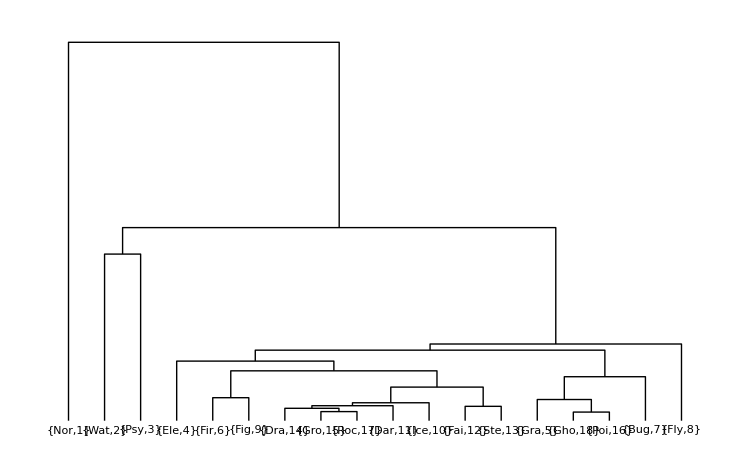

```mathematica
With[{dmat=#1},DendrogramPlot[dmat,LeafLabels->( {StringTake[#,3]&@pkmntypecorrelation[[1,#]],#}&@Position[dmat,#][[1,1]] &),Linkage->"Ward"]]&@MapIndexed[(*If[#1==0,2,If[#2[[1]]==#2[[2]],0,1/#1]]&*)#-35&,pkmntypecorrelation[[2;;]] ,{2}]
```

(Fl | Wa | Ps | No | Gr | Bu | Gr | Fi | Fi | Dr | St | Ro | Da | El | Po | Gh | Ic | Fa
2 | 4 | 4 | 11 | 3 | 11 | 3 | 1 | 5 | 7 | 1 | 3 | 3 | 5 | 1 | 1 | 2 | 1
4 | 26 | 4 | 1 | 1 | 0 | 6 | 2 | 0 | 2 | 1 | 6 | 5 | 2 | 2 | 1 | 4 | 1
4 | 4 | 25 | 1 | 2 | 0 | 1 | 6 | 3 | 4 | 4 | 2 | 1 | 0 | 0 | 0 | 1 | 3
11 | 1 | 1 | 35 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 2
3 | 1 | 2 | 1 | 14 | 3 | 1 | 3 | 0 | 1 | 1 | 1 | 2 | 1 | 6 | 5 | 2 | 1
11 | 0 | 0 | 0 | 3 | 5 | 1 | 2 | 1 | 0 | 7 | 3 | 0 | 1 | 5 | 1 | 0 | 0
3 | 6 | 1 | 1 | 1 | 1 | 6 | 0 | 3 | 4 | 2 | 2 | 1 | 1 | 2 | 1 | 1 | 0
1 | 2 | 6 | 1 | 3 | 2 | 0 | 10 | 4 | 0 | 3 | 1 | 2 | 0 | 1 | 0 | 0 | 0
5 | 0 | 3 | 1 | 0 | 1 | 3 | 4 | 11 | 2 | 1 | 1 | 2 | 1 | 0 | 1 | 0 | 0
7 | 2 | 4 | 0 | 1 | 0 | 4 | 0 | 2 | 3 | 1 | 1 | 1 | 2 | 1 | 2 | 3 | 1
1 | 1 | 4 | 0 | 1 | 7 | 2 | 3 | 1 | 1 | 4 | 3 | 1 | 1 | 0 | 2 | 0 | 3
3 | 6 | 2 | 0 | 1 | 3 | 2 | 1 | 1 | 1 | 3 | 4 | 2 | 0 | 0 | 0 | 1 | 3
3 | 5 | 1 | 0 | 2 | 0 | 1 | 2 | 2 | 1 | 1 | 2 | 7 | 0 | 2 | 3 | 1 | 0
5 | 2 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 2 | 1 | 0 | 0 | 14 | 0 | 1 | 1 | 1
1 | 2 | 0 | 0 | 6 | 5 | 2 | 1 | 0 | 1 | 0 | 0 | 2 | 0 | 6 | 2 | 0 | 0
1 | 1 | 0 | 0 | 5 | 1 | 1 | 0 | 1 | 2 | 2 | 0 | 3 | 1 | 2 | 5 | 1 | 0
2 | 4 | 1 | 0 | 2 | 0 | 1 | 0 | 0 | 3 | 0 | 1 | 1 | 1 | 0 | 1 | 8 | 0
1 | 1 | 3 | 2 | 1 | 0 | 0 | 0 | 0 | 1 | 3 | 3 | 0 | 1 | 0 | 0 | 0 | 7)

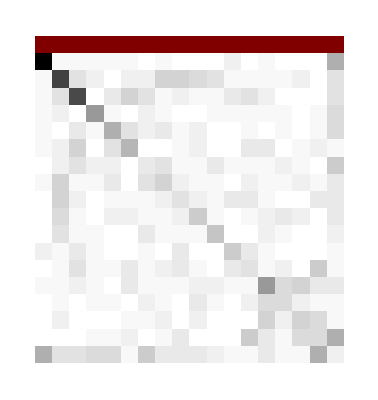

```mathematica
With[{p=#1},With[{o=Ordering[p[[2;;]],All,Total@#1>Total@#2&]},{StringTake[#,2]&/@p[[1,o]]}~Join~p[[o+1,o]] ] ]&@pkmntypecorrelation//MatrixForm
With[{p=#1},With[{o= {1,2,3,4,6,9,14,15,17,11,10,12,13,5,18,16,7,8}},{StringTake[#,3]&/@p[[1,o]]}~Join~p[[o+1,o]] ] ]&@pkmntypecorrelation//ArrayPlot
```

### Raw Type Similarities and Rankings (forms the basis for most other pokemon things)

```mathematica
Show[MapIndexed[Graphics3D[{typecolors[[#2[[1]] ]],PointSize[Large],Point[#1]}]&,PrincipalComponents[Transpose@typechart][[;;,;;3]]] ,Axes->True,AxesOrigin->{0,0,0}]
```

```mathematica
{Transpose@({types}~Join~Transpose@#)&[
{Count[#,"*"],Count[#,""],Count[#,"-"],Count[#,"X"]}&/@(typechart/.{1->"",2->"*",0->"X",0.5->"-"})
]//SortBy[#,-1*{0,2,1,-2,-2}.#&]&//MatrixForm,
Transpose@({types}~Join~Transpose@#)&[
{Count[#,"*"],Count[#,""],Count[#,"-"],Count[#,"X"]}&/@Transpose@(typechart/.{1->"",2->"*",0->"X",0.5->"-"})
]//SortBy[#,-1*{0,-1.25,0,1,1.5}.#&]&//MatrixForm
}
```

{(Ghost | 2 | 14 | 1 | 1
Ground | 5 | 10 | 2 | 1
Dragon | 1 | 15 | 1 | 1
Rock | 4 | 11 | 3 | 0
Fairy | 3 | 12 | 3 | 0
Flying | 3 | 12 | 3 | 0
Water | 3 | 12 | 3 | 0
Dark | 2 | 13 | 3 | 0
Psychic | 2 | 13 | 2 | 1
Fire | 4 | 10 | 4 | 0
Ice | 4 | 10 | 4 | 0
Normal | 0 | 15 | 2 | 1
Steel | 3 | 11 | 4 | 0
Electric | 2 | 12 | 3 | 1
Fighting | 5 | 7 | 5 | 1
Poison | 2 | 11 | 4 | 1
Bug | 3 | 8 | 7 | 0
Grass | 3 | 8 | 7 | 0),(Steel | 3 | 4 | 10 | 1
Ghost | 2 | 12 | 2 | 2
Poison | 2 | 11 | 5 | 0
Fire | 3 | 9 | 6 | 0
Fairy | 2 | 12 | 3 | 1
Electric | 1 | 14 | 3 | 0
Water | 2 | 12 | 4 | 0
Flying | 3 | 11 | 3 | 1
Dragon | 3 | 11 | 4 | 0
Normal | 1 | 16 | 0 | 1
Dark | 3 | 12 | 2 | 1
Ground | 3 | 12 | 2 | 1
Bug | 3 | 12 | 3 | 0
Fighting | 3 | 12 | 3 | 0
Psychic | 3 | 13 | 2 | 0
Grass | 5 | 9 | 4 | 0
Rock | 5 | 9 | 4 | 0
Ice | 4 | 13 | 1 | 0)}

```mathematica
dmat = DistanceMatrix[typechart];
```

```mathematica
{({MapThread[Style[StringTake[#1,1],#2,Bold]&,{types,typecolors}]}~Join~(typechart/.{1->"",2->"⊙",0->"x",0.5->"≈"}))//MatrixForm,
({MapThread[Style[StringTake[#1,1],#2,Bold]&,{types,typecolors}]}~Join~(typechart/.{1->"",2->"⊙",0->"x",0.5->"≈"}))[[{1,2,9,11,3,7,19,16,13,5,14,12,15,17,10,8,4,18,6},{1,8,10,2,6,18,15,12,4,13,11,14,16,9,7,3,17,5}]]//MatrixForm,
({MapThread[Style[StringTake[#1,1],#2,Bold]&,{types,typecolors}]}~Join~(typechart/.{1->"",2->"⊙",0->"x",0.5->"≈"}))[[ {1,2,17,7,14,10,18,3,9,4,5,16,12,15,19,8,6,11,13},{1,16,6,13,9,17,2,8,3,4,15,11,14,18,7,5,10,12} ]]//MatrixForm}
```

{(N | F | W | E | G | I | F | P | G | F | P | B | R | G | D | D | S | F
 |  |  |  |  |  |  |  |  |  |  |  | ≈ | x |  |  | ≈ | 
 | ≈ | ≈ |  | ⊙ | ⊙ |  |  |  |  |  | ⊙ | ≈ |  | ≈ |  | ⊙ | 
 | ⊙ | ≈ |  | ≈ |  |  |  | ⊙ |  |  |  | ⊙ |  | ≈ |  |  | 
 |  | ⊙ | ≈ | ≈ |  |  |  | x | ⊙ |  |  |  |  | ≈ |  |  | 
 | ≈ | ⊙ |  | ≈ |  |  | ≈ | ⊙ | ≈ |  | ≈ | ⊙ |  | ≈ |  | ≈ | 
 | ≈ | ≈ |  | ⊙ | ≈ |  |  | ⊙ | ⊙ |  |  |  |  | ⊙ |  | ≈ | 
⊙ |  |  |  |  | ⊙ |  | ≈ |  | ≈ | ≈ | ≈ | ⊙ | x |  | ⊙ | ⊙ | ≈
 |  |  |  | ⊙ |  |  | ≈ | ≈ |  |  |  | ≈ | ≈ |  |  | x | ⊙
 | ⊙ |  | ⊙ | ≈ |  |  | ⊙ |  | x |  | ≈ | ⊙ |  |  |  | ⊙ | 
 |  |  | ≈ | ⊙ |  | ⊙ |  |  |  |  | ⊙ | ≈ |  |  |  | ≈ | 
 |  |  |  |  |  | ⊙ | ⊙ |  |  | ≈ |  |  |  |  | x | ≈ | 
 | ≈ |  |  | ⊙ |  | ≈ | ≈ |  | ≈ | ⊙ |  |  | ≈ |  | ⊙ | ≈ | ≈
 | ⊙ |  |  |  | ⊙ | ≈ |  | ≈ | ⊙ |  | ⊙ |  |  |  |  | ≈ | 
x |  |  |  |  |  |  |  |  |  | ⊙ |  |  | ⊙ |  | ≈ |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  | ⊙ |  | ≈ | x
 |  |  |  |  |  | ≈ |  |  |  | ⊙ |  |  | ⊙ |  | ≈ |  | ≈
 | ≈ | ≈ | ≈ |  | ⊙ |  |  |  |  |  |  | ⊙ |  |  |  | ≈ | ⊙
 | ≈ |  |  |  |  | ⊙ | ≈ |  |  |  |  |  |  | ⊙ | ⊙ | ≈ | ),(N | P | F | F | I | F | D | B | E | R | P | G | D | G | F | W | S | G
 |  |  |  |  |  |  |  |  | ≈ |  | x |  |  |  |  | ≈ | 
 | ≈ |  |  |  | ⊙ |  |  |  | ≈ |  | ≈ |  | ≈ |  |  | x | ⊙
 |  |  |  |  |  |  | ⊙ | ≈ | ≈ |  |  |  |  | ⊙ |  | ≈ | ⊙
 |  |  | ≈ | ⊙ |  | ≈ | ⊙ |  | ≈ |  |  |  |  |  | ≈ | ⊙ | ⊙
 |  | ⊙ | ≈ | ≈ |  | ⊙ |  |  |  |  |  |  | ⊙ |  | ≈ | ≈ | ⊙
 | ≈ |  | ≈ |  |  | ⊙ |  |  |  |  |  | ⊙ |  | ⊙ |  | ≈ | 
 |  |  |  |  | x | ⊙ |  |  |  |  |  |  |  |  |  | ≈ | 
 | ≈ | ≈ | ≈ |  | ≈ |  |  |  |  | ⊙ | ≈ | ⊙ |  | ≈ |  | ≈ | ⊙
 |  | ⊙ |  |  |  | ≈ |  | ≈ |  |  |  |  | x |  | ⊙ |  | ≈
 |  | ⊙ | ⊙ | ⊙ |  |  | ⊙ |  |  |  |  |  | ≈ | ≈ |  | ≈ | 
 | ⊙ |  |  |  |  |  |  |  |  | ≈ |  | x |  | ⊙ |  | ≈ | 
x |  |  |  |  |  |  |  |  |  | ⊙ | ⊙ | ≈ |  |  |  |  | 
 |  |  |  |  | ≈ |  |  |  |  | ⊙ | ⊙ | ≈ |  | ≈ |  |  | 
 | ⊙ | x | ⊙ |  |  |  | ≈ | ⊙ | ⊙ |  |  |  |  |  |  | ⊙ | ≈
⊙ | ≈ | ≈ |  | ⊙ | ≈ |  | ≈ |  | ⊙ | ≈ | x | ⊙ |  |  |  | ⊙ | 
 |  |  | ⊙ |  |  | ≈ |  |  | ⊙ |  |  |  | ⊙ |  | ≈ |  | ≈
 |  |  | ≈ | ⊙ | ⊙ |  |  | ≈ | ⊙ |  |  |  |  |  | ≈ | ≈ | 
 | ≈ | ≈ | ≈ |  |  | ≈ | ≈ |  | ⊙ |  |  |  | ⊙ |  | ⊙ | ≈ | ≈),(N | D | I | R | G | S | F | P | W | E | D | P | G | F | F | G | F | B
 |  |  | ≈ |  | ≈ |  |  |  |  |  |  | x |  |  |  |  | 
 | ≈ |  |  |  |  |  |  |  |  |  | ⊙ | ⊙ | ≈ | ≈ |  |  | 
 |  | ≈ |  | ⊙ | ≈ | ≈ |  | ≈ |  | ⊙ |  |  |  |  | ⊙ | ⊙ | 
 |  | ⊙ |  | ≈ | ≈ | ⊙ |  |  |  |  |  |  |  | ≈ |  | ⊙ | ⊙
 |  |  | ⊙ |  | ⊙ | ⊙ | ⊙ |  | ⊙ |  |  |  |  |  | ≈ | x | ≈
 |  | ⊙ | ⊙ |  | ≈ | ≈ |  | ≈ | ≈ |  |  |  | ⊙ |  |  |  | 
 |  | ⊙ | ≈ |  | ⊙ | ≈ |  | ≈ |  | ≈ |  |  |  |  | ⊙ |  | ⊙
 |  |  | ≈ | ≈ | x |  | ≈ |  |  |  |  | ≈ | ⊙ |  | ⊙ |  | 
 |  |  | ⊙ | ⊙ |  | ⊙ |  | ≈ |  | ≈ |  |  |  |  | ≈ |  | 
 |  |  |  | x |  |  |  | ⊙ | ≈ | ≈ |  |  |  |  | ≈ | ⊙ | 
 |  |  |  |  | ≈ |  |  |  |  | ⊙ |  |  | x |  |  |  | 
 | x |  |  |  | ≈ |  | ⊙ |  |  |  | ≈ |  |  | ⊙ |  |  | 
x | ≈ |  |  |  |  |  |  |  |  |  | ⊙ | ⊙ |  |  |  |  | 
 | ⊙ |  |  |  | ≈ | ≈ | ≈ |  |  | ⊙ |  |  |  | ⊙ |  |  | 
⊙ | ⊙ | ⊙ | ⊙ |  | ⊙ |  | ≈ |  |  |  | ≈ | x | ≈ |  |  | ≈ | ≈
 |  |  | ⊙ | ⊙ | ≈ | ≈ | ≈ | ⊙ |  | ≈ |  |  |  |  | ≈ | ≈ | ≈
 |  |  | ≈ |  | ≈ |  |  |  | ≈ |  |  |  |  | ⊙ | ⊙ |  | ⊙
 | ⊙ |  |  |  | ≈ | ≈ | ≈ |  |  |  | ⊙ | ≈ | ≈ | ≈ | ⊙ | ≈ | )}

```mathematica
With[{mat=#1,edges=kruskal@#1},
Graph[#[[1]]<->#[[2]]&/@edges,
ImagePadding->10,GraphLayout->"SpringEmbedding",
VertexLabels->MapIndexed[#2[[1]]->#1&,types] ,
EdgeWeight->(Part@@Flatten[{{mat},#},1]&/@edges)
]
]&[DistanceMatrix@(Transpose@typechart/.{0->-2,0.5->-1,1->0,2->1}) ]
```

Agglomerate::ties: 4 ties have been detected; reordering input may produce a different result.

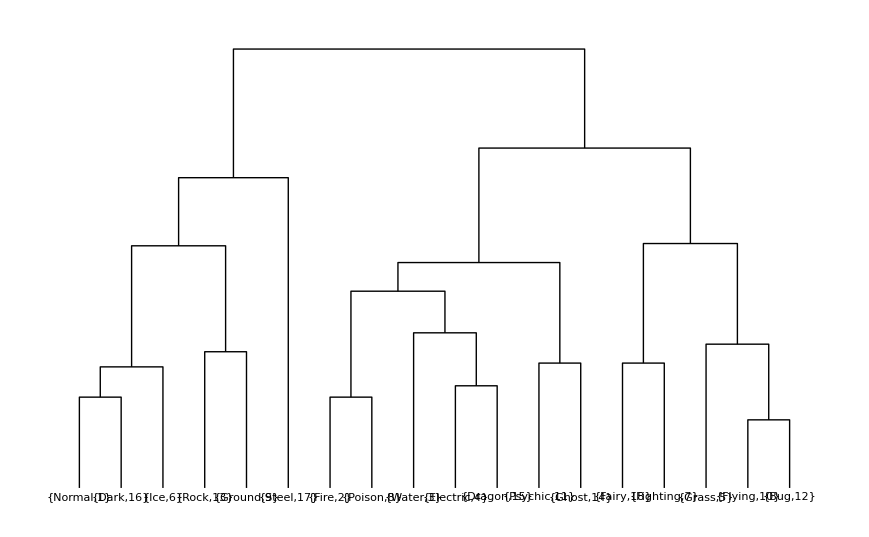

```mathematica
With[{t=#1},DendrogramPlot[t,LeafLabels->({types[[Position[t,#][[1,1]] ]],Position[t,#][[1,1]]}&),Linkage->"Ward"]]&@(Transpose@typechart/.{0->-2,0.5->-1,1->0,2->1})
ArrayPlot@DistanceMatrix@typechart[[{1,8,10,2,6,18,15,12,4,13,11,14,16,9,7,3,17,5}]]
```

#### 2-Type Defense Viability

```mathematica
pkmntypecount = Dispatch[#[[1]]->#[[2]]&/@Tally[If[Length@#==2,StringJoin[#[[1]],"-",#[[2]]]&@Sort@#,#[[1]]]&/@pkmn[[;;,2,1]]]];
defdbltypechart=DeleteDuplicates@Flatten[#,1]&@
Outer[If[#1[[1]]==#2[[1]],MapAt[Style[#,typecolors[[ Position[types,#][[1,1]]  ]],Bold]&,#1,{1}],{Row[{Style[#,typecolors[[ Position[types,#][[1,1]]  ]],Bold]&@#1,"-",Style[#,typecolors[[ Position[types,#][[1,1]]  ]],Bold]&@#2}]&@@Sort[{#1[[1]],#2[[1]]}]}~Join~(#1[[2;;]]*#2[[2;;]]) ]&,#,#,1]&@
Transpose[{types}~Join~typechart];
dbltypechart=DeleteDuplicates@Flatten[#,1]&@
Outer[If[#1[[1]]==#2[[1]],#1,{#1<>"-"<>#2&@@Sort[{#1[[1]],#2[[1]]}]}~Join~(#1[[2;;]]*#2[[2;;]]) ]&,#,#,1]&@
Transpose[{types}~Join~typechart];
```

```mathematica
(* Weighted score by the # of types resisted/weak/neutral/immune (4x vs 2x and 0.25 vs 0.5 are weighted differently) etc *)
SortBy[#,-#[[-2]]&]&@(#~Join~{(* weights-> *){0,-2,-1.5,0,1,1.5,1.75}.#,If[Head@#===String,0,#]&@(If[Length@#[[1]]>1,StringJoin[#1,"-",#2]&@@#[[1,{1,3},1]], #[[1]] ]&@#[[1]]/.pkmntypecount)}&@{#[[1]],Count[#,"O"],Count[#,"*"],Count[#,""],Count[#,"-"],Count[#,"="],Count[#,"X"]}&/@
(#/.{4->"O",2->"*",1->"",1.->"",0.5->"-",0.25->"=",0->"X",0.->"X"}))&@defdbltypechart//TableForm[#,TableHeadings->{Range[Length@defdbltypechart],{"Type","4x","2x","1x","1/2x","1/4x","0x","Score","#"}}]&
```

| Type | 4x | 2x | 1x | 1/2x | 1/4x | 0x | Score | #
1 | Fairy-Steel | 0 | 2 | 5 | 8 | 1 | 2 | 10. | 3
2 | Flying-Steel | 0 | 2 | 6 | 6 | 2 | 2 | 9.5 | 1
3 | Electric-Steel | 1 | 2 | 3 | 9 | 2 | 1 | 8.75 | 1
4 | Ghost-Steel | 0 | 4 | 2 | 8 | 1 | 3 | 8.75 | 2
5 | Poison-Steel | 1 | 1 | 6 | 6 | 3 | 1 | 8.75 | 0
6 | Normal-Steel | 1 | 2 | 3 | 10 | 0 | 2 | 8.5 | 0
7 | Bug-Steel | 1 | 0 | 8 | 7 | 1 | 1 | 8.25 | 7
8 | Dragon-Steel | 0 | 2 | 6 | 8 | 1 | 1 | 8.25 | 1
9 | Fire-Steel | 1 | 2 | 5 | 4 | 5 | 1 | 8.25 | 1
10 | Steel-Water | 0 | 3 | 4 | 8 | 2 | 1 | 8.25 | 1
11 | Grass-Steel | 1 | 1 | 6 | 8 | 1 | 1 | 7.75 | 1
12 | Dark-Steel | 1 | 2 | 4 | 9 | 0 | 2 | 7.5 | 1
13 | Steel | 0 | 3 | 4 | 10 | 0 | 1 | 7.25 | 4
14 | Fighting-Steel | 0 | 3 | 6 | 6 | 2 | 1 | 6.25 | 3
15 | Ground-Steel | 0 | 4 | 4 | 7 | 1 | 2 | 6. | 2
16 | Ghost-Normal | 0 | 1 | 12 | 2 | 0 | 3 | 5.75 | 0
17 | Psychic-Steel | 0 | 4 | 4 | 8 | 1 | 1 | 5.25 | 4
18 | Rock-Steel | 2 | 1 | 6 | 6 | 2 | 1 | 5.25 | 3
19 | Dark-Ghost | 0 | 1 | 13 | 1 | 0 | 3 | 4.75 | 3
20 | Ice-Steel | 2 | 1 | 6 | 7 | 1 | 1 | 4.75 | 0
21 | Electric-Poison | 1 | 1 | 8 | 8 | 0 | 0 | 4.5 | 0
22 | Dark-Poison | 0 | 1 | 12 | 4 | 0 | 1 | 4.25 | 2
23 | Electric-Ghost | 0 | 3 | 8 | 5 | 0 | 2 | 4. | 1
24 | Electric-Fairy | 0 | 2 | 10 | 5 | 0 | 1 | 3.75 | 1
25 | Electric-Flying | 0 | 2 | 10 | 5 | 0 | 1 | 3.75 | 5
26 | Fairy-Ghost | 0 | 2 | 12 | 0 | 1 | 3 | 3.75 | 0
27 | Fire-Flying | 1 | 2 | 8 | 4 | 2 | 1 | 3.75 | 5
28 | Ground-Water | 1 | 0 | 12 | 4 | 0 | 1 | 3.75 | 6
29 | Electric-Fire | 1 | 2 | 7 | 7 | 1 | 0 | 3.5 | 1
30 | Fire-Ghost | 0 | 5 | 4 | 6 | 1 | 2 | 3.5 | 1
31 | Ghost-Water | 0 | 4 | 6 | 6 | 0 | 2 | 3.5 | 1
32 | Poison-Water | 0 | 3 | 7 | 8 | 0 | 0 | 3.5 | 2
33 | Fairy-Fire | 0 | 4 | 6 | 6 | 1 | 1 | 3.25 | 0
34 | Fairy-Poison | 0 | 3 | 9 | 3 | 2 | 1 | 3.25 | 0
35 | Fairy-Water | 0 | 3 | 8 | 6 | 0 | 1 | 3.25 | 1
36 | Fire-Ground | 1 | 1 | 10 | 5 | 0 | 1 | 3.25 | 3
37 | Flying-Water | 1 | 1 | 10 | 5 | 0 | 1 | 3.25 | 4
38 | Fire-Poison | 1 | 3 | 6 | 5 | 3 | 0 | 3. | 0
39 | Flying-Ground | 1 | 1 | 11 | 3 | 0 | 2 | 3. | 3
40 | Dragon-Fairy | 0 | 4 | 6 | 7 | 0 | 1 | 2.75 | 1
41 | Normal-Poison | 0 | 2 | 11 | 4 | 0 | 1 | 2.75 | 0
42 | Electric-Water | 0 | 2 | 11 | 4 | 1 | 0 | 2.5 | 2
43 | Fairy-Normal | 0 | 2 | 12 | 2 | 0 | 2 | 2.5 | 2
44 | Ghost-Poison | 0 | 4 | 8 | 2 | 2 | 2 | 2.5 | 2
45 | Ghost | 0 | 2 | 12 | 2 | 0 | 2 | 2.5 | 5
46 | Flying-Poison | 0 | 4 | 8 | 2 | 3 | 1 | 2.25 | 1
47 | Dragon-Ghost | 0 | 5 | 5 | 6 | 0 | 2 | 2. | 2
48 | Fire-Water | 0 | 3 | 10 | 2 | 3 | 0 | 2. | 0
49 | Poison | 0 | 2 | 11 | 5 | 0 | 0 | 2. | 6
50 | Dark-Fire | 0 | 4 | 7 | 6 | 0 | 1 | 1.75 | 2
51 | Electric-Normal | 0 | 2 | 12 | 3 | 0 | 1 | 1.75 | 1
52 | Fire-Normal | 0 | 4 | 7 | 6 | 0 | 1 | 1.75 | 1
53 | Fairy | 0 | 2 | 12 | 3 | 0 | 1 | 1.75 | 7
54 | Bug-Fire | 1 | 2 | 9 | 5 | 1 | 0 | 1.5 | 1
55 | Dark-Fairy | 0 | 3 | 11 | 1 | 1 | 2 | 1.5 | 0
56 | Dragon-Fire | 0 | 3 | 10 | 3 | 2 | 0 | 1.5 | 2
57 | Dragon-Poison | 0 | 4 | 7 | 6 | 1 | 0 | 1.5 | 1
58 | Fairy-Ground | 0 | 4 | 8 | 4 | 0 | 2 | 1.5 | 0
59 | Fighting-Poison | 1 | 2 | 9 | 5 | 1 | 0 | 1.5 | 1
60 | Ghost-Psychic | 2 | 0 | 12 | 2 | 0 | 2 | 1.5 | 0
61 | Electric | 0 | 1 | 14 | 3 | 0 | 0 | 1.5 | 14
62 | Fire | 0 | 3 | 9 | 6 | 0 | 0 | 1.5 | 11
63 | Flying-Ghost | 0 | 5 | 7 | 2 | 1 | 3 | 1.25 | 1
64 | Ghost-Ground | 0 | 5 | 7 | 2 | 1 | 3 | 1.25 | 1
65 | Ground-Poison | 0 | 4 | 8 | 4 | 1 | 1 | 1.25 | 2
66 | Normal-Water | 0 | 3 | 10 | 4 | 0 | 1 | 1.25 | 1
67 | Bug-Electric | 0 | 2 | 12 | 4 | 0 | 0 | 1. | 1
68 | Dragon-Water | 0 | 2 | 13 | 1 | 2 | 0 | 1. | 2
69 | Fairy-Flying | 0 | 5 | 7 | 2 | 2 | 2 | 1. | 1
70 | Fighting-Ghost | 0 | 4 | 9 | 2 | 1 | 2 | 1. | 0
71 | Flying-Normal | 0 | 3 | 11 | 2 | 0 | 2 | 1. | 11
72 | Water | 0 | 2 | 12 | 4 | 0 | 0 | 1. | 26
73 | Dark-Electric | 0 | 4 | 8 | 5 | 0 | 1 | 0.75 | 0
74 | Dragon-Flying | 1 | 3 | 8 | 4 | 1 | 1 | 0.75 | 7
75 | Bug-Water | 0 | 3 | 10 | 5 | 0 | 0 | 0.5 | 0
76 | Dark-Flying | 0 | 4 | 9 | 3 | 0 | 2 | 0.5 | 3
77 | Dragon-Electric | 0 | 4 | 8 | 5 | 1 | 0 | 0.5 | 2
78 | Electric-Fighting | 0 | 3 | 10 | 5 | 0 | 0 | 0.5 | 0
79 | Fighting-Fire | 0 | 4 | 8 | 5 | 1 | 0 | 0.5 | 4
80 | Fire-Rock | 2 | 2 | 7 | 6 | 1 | 0 | 0.5 | 1
81 | Dark-Fighting | 1 | 2 | 11 | 2 | 1 | 1 | 0.25 | 2
82 | Dark-Water | 0 | 5 | 6 | 6 | 0 | 1 | 0.25 | 5
83 | Fairy-Rock | 1 | 3 | 8 | 5 | 0 | 1 | 0.25 | 3
84 | Flying | 0 | 3 | 11 | 3 | 0 | 1 | 0.25 | 2
85 | Normal | 0 | 1 | 16 | 0 | 0 | 1 | 0.25 | 35
86 | Bug-Ghost | 0 | 5 | 7 | 4 | 0 | 2 | 0. | 1
87 | Bug-Poison | 0 | 4 | 9 | 3 | 2 | 0 | 0. | 5
88 | Fire-Grass | 0 | 3 | 11 | 3 | 1 | 0 | 0. | 0
89 | Ghost-Grass | 0 | 5 | 7 | 4 | 0 | 2 | 0. | 5
90 | Poison-Psychic | 0 | 3 | 11 | 3 | 1 | 0 | 0. | 0
91 | Poison-Rock | 1 | 3 | 8 | 5 | 1 | 0 | 0. | 0
92 | Bug-Fairy | 0 | 5 | 7 | 4 | 1 | 1 | -0.25 | 0
93 | Dark-Dragon | 1 | 4 | 6 | 6 | 0 | 1 | -0.25 | 1
94 | Dragon-Ground | 1 | 2 | 11 | 3 | 0 | 1 | -0.25 | 4
95 | Dragon-Normal | 0 | 4 | 9 | 4 | 0 | 1 | -0.25 | 0
96 | Electric-Ground | 0 | 4 | 9 | 4 | 0 | 1 | -0.25 | 1
97 | Fairy-Grass | 1 | 4 | 6 | 6 | 0 | 1 | -0.25 | 1
98 | Fairy-Psychic | 0 | 3 | 12 | 1 | 1 | 1 | -0.25 | 3
99 | Normal-Psychic | 0 | 2 | 14 | 1 | 0 | 1 | -0.25 | 1
100 | Dark-Normal | 1 | 2 | 12 | 1 | 0 | 2 | -0.5 | 0
101 | Fighting-Water | 0 | 5 | 6 | 7 | 0 | 0 | -0.5 | 2
102 | Fire-Psychic | 0 | 5 | 6 | 7 | 0 | 0 | -0.5 | 3
103 | Grass-Poison | 0 | 4 | 9 | 4 | 1 | 0 | -0.5 | 6
104 | Ground-Normal | 0 | 4 | 10 | 2 | 0 | 2 | -0.5 | 1
105 | Dragon | 0 | 3 | 11 | 4 | 0 | 0 | -0.5 | 3
106 | Bug-Normal | 0 | 3 | 12 | 2 | 0 | 1 | -0.75 | 0
107 | Fairy-Fighting | 0 | 5 | 8 | 2 | 2 | 1 | -0.75 | 0
108 | Flying-Rock | 0 | 5 | 7 | 5 | 0 | 1 | -0.75 | 3
109 | Dark | 0 | 3 | 12 | 2 | 0 | 1 | -0.75 | 7
110 | Ground | 0 | 3 | 12 | 2 | 0 | 1 | -0.75 | 6
111 | Dragon-Fighting | 1 | 4 | 6 | 7 | 0 | 0 | -1. | 0
112 | Electric-Psychic | 0 | 4 | 9 | 5 | 0 | 0 | -1. | 0
113 | Electric-Rock | 1 | 3 | 9 | 4 | 1 | 0 | -1. | 0
114 | Ghost-Ice | 0 | 5 | 8 | 3 | 0 | 2 | -1. | 1
115 | Ghost-Rock | 0 | 6 | 6 | 3 | 1 | 2 | -1. | 0
116 | Grass-Water | 0 | 3 | 12 | 2 | 1 | 0 | -1. | 1
117 | Rock-Water | 1 | 3 | 9 | 4 | 1 | 0 | -1. | 6
118 | Bug-Ground | 0 | 4 | 10 | 3 | 0 | 1 | -1.25 | 1
119 | Fighting-Flying | 0 | 5 | 8 | 3 | 1 | 1 | -1.25 | 1
120 | Fighting-Normal | 0 | 4 | 10 | 3 | 0 | 1 | -1.25 | 1
121 | Bug-Fighting | 1 | 3 | 9 | 5 | 0 | 0 | -1.5 | 2
122 | Dark-Ground | 0 | 6 | 6 | 4 | 0 | 2 | -1.5 | 1
123 | Electric-Grass | 0 | 4 | 10 | 3 | 1 | 0 | -1.5 | 1
124 | Psychic-Water | 0 | 5 | 7 | 6 | 0 | 0 | -1.5 | 4
125 | Bug | 0 | 3 | 12 | 3 | 0 | 0 | -1.5 | 5
126 | Fighting | 0 | 3 | 12 | 3 | 0 | 0 | -1.5 | 10
127 | Bug-Dark | 0 | 5 | 8 | 4 | 0 | 1 | -1.75 | 0
128 | Dark-Psychic | 1 | 1 | 15 | 0 | 0 | 1 | -1.75 | 1
129 | Fairy-Ice | 1 | 3 | 10 | 3 | 0 | 1 | -1.75 | 0
130 | Bug-Dragon | 0 | 5 | 8 | 4 | 1 | 0 | -2. | 0
131 | Fire-Ice | 1 | 3 | 10 | 3 | 1 | 0 | -2. | 0
132 | Bug-Flying | 1 | 4 | 9 | 1 | 2 | 1 | -2.25 | 11
133 | Flying-Psychic | 0 | 5 | 9 | 2 | 1 | 1 | -2.25 | 4
134 | Normal-Rock | 1 | 4 | 8 | 4 | 0 | 1 | -2.25 | 0
135 | Bug-Rock | 0 | 3 | 13 | 2 | 0 | 0 | -2.5 | 3
136 | Fighting-Psychic | 0 | 3 | 13 | 2 | 0 | 0 | -2.5 | 6
137 | Ice-Poison | 0 | 5 | 8 | 5 | 0 | 0 | -2.5 | 0
138 | Psychic | 0 | 3 | 13 | 2 | 0 | 0 | -2.5 | 25
139 | Fighting-Ground | 0 | 6 | 7 | 3 | 1 | 1 | -2.75 | 0
140 | Flying-Grass | 1 | 4 | 9 | 2 | 1 | 1 | -2.75 | 3
141 | Flying-Ice | 1 | 3 | 11 | 2 | 0 | 1 | -2.75 | 2
142 | Grass-Ground | 1 | 3 | 11 | 2 | 0 | 1 | -2.75 | 1
143 | Ground-Rock | 2 | 4 | 6 | 4 | 1 | 1 | -2.75 | 2
144 | Dragon-Psychic | 0 | 6 | 6 | 6 | 0 | 0 | -3. | 4
145 | Electric-Ice | 0 | 4 | 11 | 3 | 0 | 0 | -3. | 1
146 | Dark-Grass | 1 | 6 | 4 | 6 | 0 | 1 | -3.25 | 2
147 | Dark-Rock | 1 | 6 | 4 | 6 | 0 | 1 | -3.25 | 2
148 | Grass-Normal | 0 | 6 | 7 | 4 | 0 | 1 | -3.25 | 1
149 | Ground-Psychic | 0 | 6 | 7 | 4 | 0 | 1 | -3.25 | 1
150 | Dragon-Rock | 0 | 6 | 7 | 4 | 1 | 0 | -3.5 | 1
151 | Fighting-Grass | 1 | 5 | 6 | 6 | 0 | 0 | -3.5 | 3
152 | Ice-Water | 0 | 4 | 12 | 1 | 1 | 0 | -3.5 | 4
153 | Grass | 0 | 5 | 9 | 4 | 0 | 0 | -3.5 | 14
154 | Rock | 0 | 5 | 9 | 4 | 0 | 0 | -3.5 | 4
155 | Ice-Normal | 1 | 3 | 12 | 1 | 0 | 1 | -3.75 | 0
156 | Bug-Grass | 2 | 4 | 7 | 3 | 2 | 0 | -4. | 3
157 | Bug-Ice | 2 | 2 | 11 | 3 | 0 | 0 | -4. | 0
158 | Dragon-Grass | 1 | 5 | 8 | 1 | 3 | 0 | -4. | 1
159 | Grass-Rock | 0 | 4 | 12 | 2 | 0 | 0 | -4. | 1
160 | Bug-Psychic | 0 | 6 | 8 | 3 | 1 | 0 | -4.5 | 0
161 | Dragon-Ice | 0 | 5 | 10 | 3 | 0 | 0 | -4.5 | 3
162 | Fighting-Rock | 0 | 7 | 5 | 6 | 0 | 0 | -4.5 | 1
163 | Dark-Ice | 1 | 5 | 8 | 3 | 0 | 1 | -4.75 | 1
164 | Ground-Ice | 0 | 5 | 11 | 1 | 0 | 1 | -4.75 | 1
165 | Grass-Psychic | 1 | 6 | 5 | 6 | 0 | 0 | -5. | 2
166 | Ice | 0 | 4 | 13 | 1 | 0 | 0 | -5. | 8
167 | Psychic-Rock | 0 | 7 | 6 | 5 | 0 | 0 | -5.5 | 2
168 | Fighting-Ice | 0 | 6 | 9 | 3 | 0 | 0 | -6. | 0
169 | Ice-Rock | 2 | 4 | 8 | 4 | 0 | 0 | -6. | 1
170 | Grass-Ice | 1 | 6 | 7 | 4 | 0 | 0 | -7. | 2
171 | Ice-Psychic | 0 | 6 | 10 | 2 | 0 | 0 | -7. | 1

```mathematica
DistanceMatrix@defdbltypechart[[;;,2;;]]
```

{{0,4.5,3.,1.75,6.,7.25,3.75,4.,4.5,5.5,3.25,4.5,9.,6.5,4.,7.25,9.5,4.5,6.5,7.1875,«131»,15.3125,7.5625,12.5,18.625,16.25,10.5,14.5,8.25,15.5625,11.5625,6.,14.5,5.5625,9.75,3.5,10.25,6.8125,6.5,8.5625,6.75},«170»}

```mathematica
Graph[defdbltypechart[[;;,1]],
#[[1]]<->#[[2]]/.Dispatch@MapIndexed[#2[[1]]->#1&,defdbltypechart[[;;,1]]]&/@kruskal@DistanceMatrix@defdbltypechart[[;;,2;;]],
VertexLabels->"Name"
]
```

-Graphics-

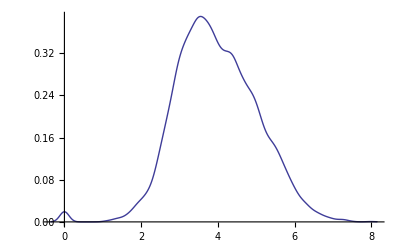

```mathematica
SmoothHistogram@Flatten@DistanceMatrix[dbltypechart,DistanceFunction->(Norm[#2[[2;;]]-#1[[2;;]]]&)]
```

```mathematica
(* Clustered Defensive Types, setup is by weight determined above. *)
(ClusterFlatten@#)[[;;,1]]&/@ClusterSplit[Agglomerate[#,DistanceFunction->(Norm[#1[[2;;]]-#2[[2;;]] ]&),Linkage->"Ward"],30]&[
(defdbltypechart/.{4->-2,2->-1.25,1->0,1.->0,0.5->1,0.25->1.25,0->1.5,0.->1.5})
]
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

{{Normal,Normal-Psychic,Dark-Poison,Electric-Normal,Electric},{Dark-Normal,Dark,Dark-Electric,Dark-Psychic,Dark-Fighting},{Grass-Rock,Ground-Ice,Dark-Ground,Dark-Rock},{Ice-Normal,Ice,Electric-Ice,Dark-Ice},{Ground-Normal,Electric-Ground,Ground,Ground-Water,Fairy-Ground,Fighting-Ground,Flying-Ground,Bug-Ground},{Normal-Rock,Rock,Electric-Rock,Ice-Rock,Ground-Rock,Fighting-Rock,Fairy-Rock},{Fire-Normal,Fire-Ice,Dark-Fire},{Fire,Electric-Fire,Fire-Poison,Fire-Psychic,Fire-Ghost},{Normal-Poison,Poison,Electric-Poison,Ice-Poison},{Fire-Ground,Ground-Poison,Fire-Rock,Poison-Rock},{Normal-Water,Water,Ice-Water,Dark-Water,Electric-Water,Rock-Water},{Psychic-Water,Ghost-Water,Fire-Water,Poison-Water,Fighting-Water,Fairy-Water},{Dragon-Psychic,Dragon-Ghost,Bug-Dragon,Dragon-Flying},{Dragon-Normal,Dark-Dragon,Dragon-Ice,Dragon-Rock,Dragon-Ground,Dragon,Dragon-Electric,Dragon-Water,Dragon-Fighting,Dragon-Fire,Dragon-Poison},{Ghost-Grass,Grass-Psychic,Bug-Psychic},{Electric-Psychic,Psychic,Ice-Psychic},{Ghost-Normal,Dark-Ghost,Bug-Rock,Flying-Rock},{Psychic-Rock,Ghost-Rock,Ground-Psychic,Ghost-Ground},{Bug-Ghost,Ghost-Ice,Ghost-Poison,Poison-Psychic,Ghost-Psychic,Ghost,Electric-Ghost},{Dark-Fairy,Fairy-Normal,Fairy,Fairy-Ice,Dragon-Fairy,Fairy-Fighting,Fairy-Ghost,Fairy-Psychic,Bug-Fairy,Fairy-Flying},{Fairy-Fire,Electric-Fairy,Fairy-Poison},{Fighting-Normal,Fighting,Electric-Fighting,Fighting-Ice,Fighting-Fire,Fighting-Poison},{Fighting-Psychic,Fighting-Ghost,Bug-Fighting,Fighting-Flying},{Grass-Normal,Dark-Grass,Grass-Ice,Grass-Water,Electric-Grass,Grass,Grass-Ground,Dragon-Grass,Flying-Grass,Bug-Grass,Fairy-Grass,Fighting-Grass},{Flying-Normal,Flying,Electric-Flying,Flying-Poison,Bug-Flying,Flying-Psychic,Flying-Ghost},{Fire-Flying,Bug-Fire,Flying-Water,Bug-Water},{Bug-Normal,Bug,Flying-Ice,Bug-Ice,Dark-Flying,Bug-Dark},{Fire-Grass,Bug-Electric,Bug-Poison,Grass-Poison},{Fairy-Steel,Poison-Steel,Fighting-Steel,Steel-Water,Normal-Steel,Dark-Steel,Electric-Steel,Steel,Ice-Steel,Dragon-Steel,Grass-Steel,Ground-Steel,Fire-Steel,Rock-Steel},{Ghost-Steel,Psychic-Steel,Flying-Steel,Bug-Steel}}

### Pokemon Groups by Base Stats (Arceus normalized total, direction vector)

```mathematica
ClusterFlatten/@ClusterSplit[#,35]&@Agglomerate[({N@Total@#/720}~Join~N@Normalize@#&/@pkmn[[;;,2,-1]])->pkmn[[;;,1]],Linkage->"Ward"]
```

Agglomerate::ties: 2 ties have been detected; reordering input may produce a different result.

{1,2,6,6,7,7,8,9,9,10,10,10,10,11,12,12,12,12,13,14,14,14,15,15,16,16,17,18,19,19,19,19,23,25,25}

```mathematica
communities=FindGraphCommunities@System`Graph[Range[Length@pkmn],#[[1]]<->#[[2]]&/@
DeleteDuplicates[Sort/@Select[Flatten[MapIndexed[If[And[#1≤0.012,#1≠0],#2,0]&,DistanceMatrix@({Total@#/720}~Join~N@Normalize@#&/@pkmn[[;;,2,-1]]) ,{2}],1],Head@#===List&] ],
VertexLabels->MapIndexed[#2[[1]]->#1&,pkmn[[;;,1]]] 
];
```

```mathematica
#~Join~{Abs[#[[3]]-#[[1]] ]}&@Flatten[{N@Median@#,N@Max@#-Min@#}&/@#]&/@Transpose@{Transpose@# ,Transpose@#[[communities[[#2]]]] }&[({Total@#/720}~Join~N@Normalize@#&/@pkmn[[;;,2,-1]]),3]//TableForm
```

0.694444 | 0.755556 | 0.729167 | 0.326389 | 0.0347222
0.3618 | 0.876368 | 0.370625 | 0.196607 | 0.00882473
0.428261 | 0.743198 | 0.362379 | 0.180289 | 0.0658816
0.374634 | 0.776825 | 0.409182 | 0.182379 | 0.0345474
0.408248 | 0.621987 | 0.454569 | 0.209349 | 0.0463204
0.383991 | 0.682036 | 0.464173 | 0.100717 | 0.0801825
0.371339 | 0.743607 | 0.355403 | 0.124517 | 0.0159358

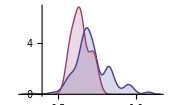
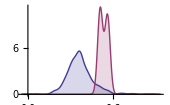
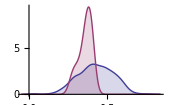
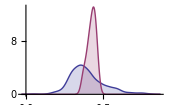
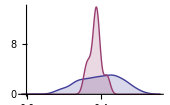
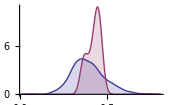
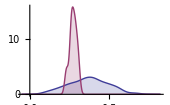

```mathematica
SmoothHistogram[#,Filling->Axis,ImageSize->170]&/@Transpose@{Transpose@# ,Transpose@#[[communities[[#2]]]] }&[({Total@#/720}~Join~N@Normalize@#&/@pkmn[[;;,2,-1]]),10]
```

```mathematica
communities[[1]]/.MapIndexed[#2[[1]]->#1&,pkmn[[;;,1]] ]
```

{Charizard,Venomoth,Golduck,Gengar,Jolteon,Zapdos,Typhlosion,Xatu,Espeon,Girafarig,Raikou,Gardevoir,Manectric,Latios,Roserade,Cherrim,Mismagius,Yanmega,Darkrai,Liepard,Swoobat,Lilligant,Sigilyph,Galvantula,Volcarona,Keldeo,Delphox,Pyroar,Heliolisk,Dedenne,Mega Pidgeot,Mega Houndoom,Mega Manectric,Tornadus (Therian Forme)}

```mathematica
MatrixForm/@( communities/.MapIndexed[#2[[1]]->#1&,pkmn[[;;,1]] ]  )
```

{(Charizard
Venomoth
Golduck
Gengar
Jolteon
Zapdos
Typhlosion
Xatu
Espeon
Girafarig
Raikou
Gardevoir
Manectric
Latios
Roserade
Cherrim
Mismagius
Yanmega
Darkrai
Liepard
Swoobat
Lilligant
Sigilyph
Galvantula
Volcarona
Keldeo
Delphox
Pyroar
Heliolisk
Dedenne
Mega Pidgeot
Mega Houndoom
Mega Manectric
Tornadus (Therian Forme)),(Pidgeot
Raticate
Fearow
Raichu
Persian
Primeape
Dodrio
Aerodactyl
Crobat
Stantler
Sceptile
Volbeat
Zangoose
Floatzel
Ambipom
Purugly
Froslass
Simisage
Simisear
Simipour
Zebstrika
Basculin
Cinccino
Swanna
Sawsbuck
Emolga
Greninja
Talonflame
Hawlucha),(Venusaur
Blastoise
Butterfree
Clefable
Dewgong
Articuno
Meganium
Politoed
Kingdra
Suicune
Ludicolo
Masquerain
Altaria
Lunatone
Chimecho
Magmortar
Mesprit
Heatran
Vanilluxe
Jellicent
Mega Venusaur
Mega Blastoise
Mega Altaria),(Arcanine
Moltres
Dragonite
Tyranitar
Blaziken
Salamence
Infernape
Lucario
Azelf
Archeops
Mienshao
Hydreigon
Genesect
Mega Charizard X
Mega Swampert
Mega Sharpedo
Mega Absol
Mega Glalie
Tornadus (Incarnate Forme)
Thundurus (Incarnate Forme)
Thundurus (Therian Forme)
Landorus (Incarnate Forme)
Landorus (Therian Forme)),(Nidoqueen
Poliwrath
Farfetch'd
Seaking
Ditto
Feraligatr
Heracross
Delcatty
Spinda
Castform
Glalie
Phione
Stoutland
Sawk
Garbodor
Slurpuff
Malamar),(Victreebel
Exeggutor
Octillery
Shiftry
Camerupt
Cacturne
Seviper
Luxray
Mothim
Toxicroak
Carnivine
Samurott
Maractus
Eelektross
Heatmor),(Swampert
Torterra
Drapion
Leafeon
Gliscor
Crustle
Klinklang
Chesnaught
Barbaracle
Tyrantrum
Gourgeist (Small Size)
Gourgeist (Average Size)
Gourgeist (Large Size)
Gourgeist (Super Size)),(Arbok
Qwilfish
Mightyena
Solrock
Staraptor
Bibarel
Kricketune
Mamoswine
Watchog
Unfezant
Krookodile
Braviary),(Machamp
Granbull
Ursaring
Armaldo
Beartic
Druddigon
Golurk
Pangoro
Trevenant),(Azumarill
Dunsparce
Swalot
Whiscash
Tropius
Walrein
Lickilicky
Audino),(Bellossom
Corsola
Cradily
Vespiquen
Bronzong
Wormadam (Plant Cloak)
Wormadam (Trash Cloak)),(Nidoking
Rapidash
Flygon
Leavanny
Mega Medicham),(Vileplume
Ampharos
Empoleon
Beheeyem
Clawitzer),(Entei
Garchomp
Terrakion
Mega Kangaskhan
Meloetta (Pirouette Forme)),(Kyogre
Dialga
Palkia
Reshiram
Mega Latios),(Pinsir
Kabutops
Scizor
Bisharp),(Slowking
Gastrodon
Amoonguss
Aromatisse),(Groudon
Zekrom
Mega Garchomp
Kyurem (Black Kyurem)),(Xerneas
Yveltal
Giratina (Origin Forme)
Kyurem (Normal Kyurem)),(Ninetales
Medicham
Lumineon),(Lapras
Vaporeon
Aurorus),(Exploud
Seismitoad
Gogoat),(Tentacruel
Virizion),(Golem
Donphan),(Marowak
Wormadam (Sandy Cloak)),(Hitmonchan
Hitmontop),(Tauros
Scolipede),(Furret
Linoone),(Jumpluff
Pachirisu),(Minun
Illumise),(Banette
Absol),(Honchkrow
Emboar),(Chatot
Vivillon),(Magnezone
Glaceon),(Carbink
Aegislash (Shield Forme)),(Mega Mewtwo X
Mega Rayquaza),(Mega Steelix
Mega Aggron),(Mega Blaziken
Mega Lucario),(Beedrill),(Sandslash),(Wigglytuff),(Parasect),(Dugtrio),(Alakazam),(Slowbro),(Muk),(Cloyster),(Hypno),(Kingler),(Electrode),(Hitmonlee),(Weezing),(Kangaskhan),(Starmie),(Mr.Mime),(Jynx),(Gyarados),(Flareon),(Omastar),(Snorlax),(Mewtwo),(Mew),(Noctowl),(Ledian),(Ariados),(Lanturn),(Sudowoodo),(Sunflora),(Quagsire),(Umbreon),(Unown),(Wobbuffet),(Forretress),(Steelix),(Shuckle),(Magcargo),(Delibird),(Mantine),(Skarmory),(Houndoom),(Smeargle),(Miltank),(Blissey),(Lugia),(Ho-Oh),(Celebi),(Beautifly),(Dustox),(Swellow),(Pelipper),(Breloom),(Slaking),(Ninjask),(Shedinja),(Hariyama),(Sableye),(Mawile),(Aggron),(Plusle),(Sharpedo),(Wailord),(Torkoal),(Grumpig),(Crawdaunt),(Claydol),(Milotic),(Kecleon),(Huntail),(Gorebyss),(Relicanth),(Luvdisc),(Metagross),(Regirock),(Regice),(Registeel),(Latias),(Rayquaza),(Jirachi),(Rampardos),(Bastiodon),(Drifblim),(Lopunny),(Skuntank),(Spiritomb),(Hippowdon),(Abomasnow),(Weavile),(Rhyperior),(Tangrowth),(Electivire),(Togekiss),(Porygon-Z),(Gallade),(Probopass),(Dusknoir),(Uxie),(Regigigas),(Cresselia),(Manaphy),(Arceus),(Victini),(Serperior),(Musharna),(Gigalith),(Excadrill),(Conkeldurr),(Throh),(Whimsicott),(Scrafty),(Cofagrigus),(Carracosta),(Zoroark),(Gothitelle),(Reuniclus),(Escavalier),(Alomomola),(Ferrothorn),(Chandelure),(Haxorus),(Cryogonal),(Accelgor),(Stunfisk),(Bouffalant),(Mandibuzz),(Durant),(Cobalion),(Diggersby),(Florges),(Furfrou),(Meowstic),(Dragalge),(Sylveon),(Goodra),(Klefki),(Avalugg),(Noivern),(Zygarde),(Diancie),(Mega Charizard Y),(Mega Beedrill),(Mega Alakazam),(Mega Slowbro),(Mega Gengar),(Mega Pinsir),(Mega Gyarados),(Mega Aerodactyl),(Mega Mewtwo Y),(Mega Ampharos),(Mega Scizor),(Mega Heracross),(Mega Tyranitar),(Mega Sceptile),(Mega Gardevoir),(Mega Sableye),(Mega Mawile),(Mega Camerupt),(Mega Banette),(Mega Salamence),(Mega Metagross),(Mega Latias),(Primal Kyogre),(Primal Groudon),(Deoxys (Normal Forme)),(Deoxys (Attack Forme)),(Deoxys (Defense Forme)),(Deoxys (Speed Forme)),(Mega Lopunny),(Mega Abomasnow),(Mega Gallade),(Rotom (Normal Rotom)),(Rotom (Heat Rotom)),(Rotom (Wash Rotom)),(Rotom (Frost Rotom)),(Rotom (Fan Rotom)),(Rotom (Mow Rotom)),(Giratina (Altered Forme)),(Shaymin (Land Forme)),(Shaymin (Sky Forme)),(Mega Audino),(Darmanitan (Standard Mode)),(Darmanitan (Zen Mode)),(Kyurem (White Kyurem)),(Meloetta (Aria Forme)),(Aegislash (Blade Forme)),(Mega Diancie)}